## I. Loading package

```mathematica
<<xAct`xBrauer`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

xAct`SymmetricFunctions  version 1.0.0, {2023,24,2}

Copyright (C) 2020-2022, Thomas Helpin, under the General Public License.

------------------------------------------------------------

xAct`BrauerAlgebra  version 1.0.0, {2023,24,2}

Copyright (C) 2020-2022, Thomas Helpin, under the General Public License.

------------------------------------------------------------

Package xAct`xBrauer`  version 0.1.0, {2022,28,10}

Copyright (C) 2020-2022, Thomas Helpin, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
Names["xAct`SymmetricFunctions`*"]
```

{BranchingRule,BratteliDiagramSn,BratteliPathSn,ChangeSymmetricBasis,CharacterSymmetricGroup,CompleteSymmetricFunction,CompleteSymmetricPolynomial,DimOfIrrep,DimOfIrrepSn,ElementarySymmetricFunction,ElementarySymmetricPolynomial,GeneralLinearGroup,IncludedPartitionQ,InverseKostkaCoefficient,InverseLittlewoodRichardsonRule,KostkaCoefficient,LittlewoodRichardsonCoefficient,LittlewoodRichardsonRule,LittlewoodRichardsonTableaux,MonomialSymmetricFunction,MonomialSymmetricPolynomial,NewellLittlewoodCoefficient,NewellLittlewoodRule,OrthogonalGroup,Output,PartitionDominatesQ,PartitionJoin,PartitionMultiplicities,Plethysm,PowerSymmetricFunction,SchurFunction,SchurPolynomial,SemiStandardTableaux,StandardTableaux,SymmetricFunctionBasis,SymmetricFunctionExpand,SymmetricFunctionQ,SymplecticGroup,TableauForm,ToPolynomial,TransposePartition,ZCoefficient,$LieGroups,$SymmetricFunctions,xAct`SymmetricFunctions`$Version}

```mathematica
Names["xAct`BrauerAlgebra`*"]
```

{AClass,BraceletForm,Bracelets,BraceletsToCentralYoung,BratteliDiagramBn,BratteliPathBn,BrauerAlgebra,BrauerBracelets,BrauerCycles,BrauerDiagram,BrauerElements,BrauerElementsCycles,BrauerGenerators,BrauerGraph,BrauerList,BrauerParameter,BrauerProduct,BrauerToPerm,CanonicalPrimitiveIdempotent,CentralIdempotent,CentralIdempotentBranching,CentralYoung,CentralYoungProjector,ConjugacyClass,ConjugacyClassProduct,ConjugacyClassRelations,ConjugacyClassSum,CosetType,CycleType,DimOfIrrepBn,DownInteger,Dressed,EigenvaluesA,ExpandCentralYoung,FactorSpace,Flip,GeneratorPerm,GeneratorTrace,HyperOctahedralGenerators,HyperOctahedralGroup,HyperOctahedralQ,IdClass,IdealSpace,IdentityBrauer,IdentityJf,InvolutionQ,IrrepsOfBrauer,JucysMurphy,JucysMurphyB,JucysMurphyS,ManifestSym,Narcs,Ncrossing,Nlines,NumberOfBracelets,OrderBrauer,PermNotation,PermToBrauer,ProductConvention,SchurWeylDual,SemiNormalYoungUnit,SetBrauerParamaterTo,SignatureBrauer,SimplifyCentralYoung,SnTracelessProjector,SplittingIdempotent,StabilityIndex,StructureConstant,SymmetricGroupOnly,SymmetricGroupQ,TClass,ToBracelets,ToBrauerCycles,ToBrauerList,ToCanonicalBracelets,ToGenerators,ToReducedWord,ToRepresentativeDiagram,TracelessProjector,TraceProjector,TransposeTableau,WeingartenO,WeingartenU,YoungSymmetrizer,ZonalPolynomialId,ZonalSpherical,xAct`BrauerAlgebra`$Version}

```mathematica
Names["xAct`xBrauer`*"]
```

{BrauerToTensor,ClassAction,ClassTensor,ContractSymplecticForm,DefSymplecticForm,ExpandClassTensor,GLCentralIrreducibleProject,GLIrreducibleProject,GLIrrepsOfTensor,GLTracelessProject,GLTracelessProjector,InducedMetricQ,MetricOfTensor,OCentralIrreducibleProject,OIrreducibleProject,OIrrepsOfTensor,SemiNormalYoungProject,SeparateSymplecticForm,SymplecticFormOfTensor,SymplecticFormQ,SymplecticFormsOfVBundle,ToClassTensor,TracelessProject,TracelessProjectorTensor,TracePermuteIndices,TraceProject,TraceProjectorTensor,VBundleOfSymplecticForm,$SymplecticForms,$Version,$xTensorVersionExpected}

## II. Geometric set-up : Riemannian manifold with metric g

```mathematica
Map[ToExpression[StringJoin["i",ToString[#]]]&,Range[16]]
```

{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16}

Definition of the manifold M with dimension a parameter  dim

```mathematica
DefManifold[M,dim,{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

Definition of a pseudo-Riemannian metric g and associated tensors.

```mathematica
Options[DefMetric]
```

{PrintAs→Identity,FlatMetric→False,InducedFrom→Null,ConformalTo→Null,OtherDependencies→{},WeightedWithBasis→Null,epsilonOrientationInBasis:>{AIndex,s_ϵ},Master→Null,ProtectNewSymbol:>$ProtectNewSymbols,DefInfo→{,},DefMetricPerturbation→True}

```mathematica
Options[DefCovD]
```

{SymbolOfCovD→{;,▽},Torsion→False,Curvature→True,FromMetric→Null,CurvatureRelations→True,ExtendedFrom→Null,OtherDependencies→{},OrthogonalTo→{},ProjectedWith→{},WeightedWithBasis→Null,ProtectNewSymbol:>$ProtectNewSymbols,Master→Null,DefInfo→{covariant derivative,},SymCovDQ→False}

```mathematica
SetOptions[DefCovD,CurvatureRelations->True]
```

{SymbolOfCovD→{;,▽},Torsion→False,Curvature→True,FromMetric→Null,CurvatureRelations→True,ExtendedFrom→Null,OtherDependencies→{},OrthogonalTo→{},ProjectedWith→{},WeightedWithBasis→Null,ProtectNewSymbol:>$ProtectNewSymbols,Master→Null,DefInfo→{covariant derivative,},SymCovDQ→False}

```mathematica
DefMetric[-1,g[-i1,-i2],cd,SymbolOfCovD->{";","∇^(g) "},PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor g[-i1,-i2].

** DefTensor: Defining antisymmetric tensor epsilong[-i1,-i10].

** DefCovD: Defining covariant derivative cd[-i1].

** DefTensor: Defining vanishing torsion tensor Torsioncd[i1,-i10,-i11].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcd[i1,-i10,-i11].

** DefTensor: Defining Riemann tensor Riemanncd[-i1,-i10,-i11,-i12].

** DefTensor: Defining symmetric Ricci tensor Riccicd[-i1,-i10].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteincd[-i1,-i10].

** DefTensor: Defining Weyl tensor Weylcd[-i1,-i10,-i11,-i12].

** DefTensor: Defining symmetric TFRicci tensor TFRiccicd[-i1,-i10].

** DefTensor: Defining Kretschmann scalar Kretschmanncd[].

** DefCovD:  Computing RiemannToWeylRules for dim d

** DefCovD:  Computing RicciToTFRicci for dim d

** DefCovD:  Computing RicciToEinsteinRules for dim d

** DefTensor: Defining symmetrized Riemann tensor SymRiemanncd[-i1,-i10,-i11,-i12].

** DefTensor: Defining symmetric Schouten tensor Schoutencd[-i1,-i10].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCcd[LI[_],-i1,-i10].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCcd[LI[_],-i1,-i10].

** DefTensor: Defining weight +2 density Detg[]. Determinant.

** DefParameter: Defining parameter PerturbationParameterg.

** DefTensor: Defining tensor Perturbationg[LI[order],-i1,-i10].

## III. Realisation of the Brauer algebra as operators on tensors and traceless projectors

### 1. BrauerToTensor for Riemannian manifolds

```mathematica
?BrauerToTensor
```

```mathematica
(********* Tensorial realisation of the elements of the Brauer algebra Subscript[B, n](δ)  **********)
```

```mathematica
BrauerElements[2];
BrauerDiagram/@%
BrauerToTensor/@%%
```

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{δ |   | i1
i3 |   δ |   | i2
i4 |  ,δ |   | i2
i3 |   δ |   | i1
i4 |  ,g | i1 | i2
  |   g |   |  
i3 | i4}

```mathematica
BrauerElements[3];
BrauerDiagram/@%
BrauerToTensor/@%%
```

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{δ |   | i1
i4 |   δ |   | i2
i5 |   δ |   | i3
i6 |  ,δ |   | i1
i4 |   δ |   | i3
i5 |   δ |   | i2
i6 |  ,δ |   | i2
i4 |   δ |   | i1
i5 |   δ |   | i3
i6 |  ,δ |   | i3
i4 |   δ |   | i1
i5 |   δ |   | i2
i6 |  ,δ |   | i2
i4 |   δ |   | i3
i5 |   δ |   | i1
i6 |  ,δ |   | i3
i4 |   δ |   | i2
i5 |   δ |   | i1
i6 |  ,δ |   | i3
i6 |   g | i1 | i2
  |   g |   |  
i4 | i5,δ |   | i3
i5 |   g | i1 | i2
  |   g |   |  
i4 | i6,δ |   | i3
i4 |   g | i1 | i2
  |   g |   |  
i5 | i6,δ |   | i2
i6 |   g | i1 | i3
  |   g |   |  
i4 | i5,δ |   | i2
i5 |   g | i1 | i3
  |   g |   |  
i4 | i6,δ |   | i2
i4 |   g | i1 | i3
  |   g |   |  
i5 | i6,δ |   | i1
i6 |   g | i2 | i3
  |   g |   |  
i4 | i5,δ |   | i1
i5 |   g | i2 | i3
  |   g |   |  
i4 | i6,δ |   | i1
i4 |   g | i2 | i3
  |   g |   |  
i5 | i6}

```mathematica
(******* Tensor realisation of the elements of the algebra of conjugacy class sums of Subscript[B, n](δ) *******)
```

```mathematica
?Bracelets
```

```mathematica
?BrauerBracelets
```

```mathematica
?BraceletForm
```

```mathematica
Options[BraceletForm]
```

{ImageSize→42,ColorRules→{1→RGBColor[1, 0, 0],2→RGBColor[Rational[255, 256], Rational[87, 128], Rational[33, 128]],3→GrayLevel[0]}}

```mathematica
BrauerBracelets[2]
BrauerToTensor/@%
```

{{{3},{3}}_◦,{{3,3}}_◦,{{1,2}}_◦}

{δ |   | i1
i3 |   δ |   | i2
i4 |  ,δ |   | i2
i3 |   δ |   | i1
i4 |  ,g | i1 | i2
  |   g |   |  
i3 | i4}

```mathematica
BrauerBracelets[3]
Head/@%
```

{{{3},{3},{3}}_◦,{{3,3},{3}}_◦,{{3,3,3}}_◦,{{1,2},{3}}_◦,{{1,2,3}}_◦}

{Bracelets,Bracelets,Bracelets,Bracelets,Bracelets}

```mathematica
BrauerBracelets[3]
BraceletForm/@%
```

{{{3},{3},{3}}_◦,{{3,3},{3}}_◦,{{3,3,3}}_◦,{{1,2},{3}}_◦,{{1,2,3}}_◦}

{{-Graphics-,-Graphics-,-Graphics-}_◦,{-Graphics-,-Graphics-}_◦,{-Graphics-}_◦,{-Graphics-,-Graphics-}_◦,{-Graphics-}_◦}

```mathematica
BrauerBracelets[3]
BrauerToTensor/@%
```

{{{3},{3},{3}}_◦,{{3,3},{3}}_◦,{{3,3,3}}_◦,{{1,2},{3}}_◦,{{1,2,3}}_◦}

{δ |   | i1
i4 |   δ |   | i2
i5 |   δ |   | i3
i6 |  ,δ |   | i3
i4 |   δ |   | i2
i5 |   δ |   | i1
i6 |  +δ |   | i1
i4 |   δ |   | i3
i5 |   δ |   | i2
i6 |  +δ |   | i2
i4 |   δ |   | i1
i5 |   δ |   | i3
i6 |  ,δ |   | i2
i4 |   δ |   | i3
i5 |   δ |   | i1
i6 |  +δ |   | i3
i4 |   δ |   | i1
i5 |   δ |   | i2
i6 |  ,δ |   | i3
i6 |   g | i1 | i2
  |   g |   |  
i4 | i5+δ |   | i2
i5 |   g | i1 | i3
  |   g |   |  
i4 | i6+δ |   | i1
i4 |   g | i2 | i3
  |   g |   |  
i5 | i6,δ |   | i2
i6 |   g | i1 | i3
  |   g |   |  
i4 | i5+δ |   | i1
i6 |   g | i2 | i3
  |   g |   |  
i4 | i5+δ |   | i3
i5 |   g | i1 | i2
  |   g |   |  
i4 | i6+δ |   | i1
i5 |   g | i2 | i3
  |   g |   |  
i4 | i6+δ |   | i3
i4 |   g | i1 | i2
  |   g |   |  
i5 | i6+δ |   | i2
i4 |   g | i1 | i3
  |   g |   |  
i5 | i6}

```mathematica
(****** The Bracelets objects can be expressed with the SymH notation of the SymManipulator Package ******)
```

```mathematica
?SymH
```

```mathematica
BrauerBracelets[3]
BrauerToTensor[#,Output->SymH]&/@%
```

{{{3},{3},{3}}_◦,{{3,3},{3}}_◦,{{3,3,3}}_◦,{{1,2},{3}}_◦,{{1,2,3}}_◦}

{Sym_(123456)[δδδ] |   | i1 |   | i2 |   | i3
i4 |   | i5 |   | i6 |  ,3 Sym_(123456)[δδδ] |   | i2 |   | i1 |   | i3
i4 |   | i5 |   | i6 |  ,2 Sym_(123456)[δδδ] |   | i3 |   | i1 |   | i2
i4 |   | i5 |   | i6 |  ,3 Sym_(123456)[δgg] |   | i3 | i1 | i2 |   |  
i6 |   |   |   | i4 | i5,6 Sym_(123456)[δgg] |   | i3 | i1 | i2 |   |  
i4 |   |   |   | i5 | i6}

### 2. Traceless projectors

```mathematica
?TracelessProjectorTensor
```

#### 2.1. Projectors for tensors of order 3

##### a. The projector for tensors with arbitrary symmetries

```mathematica
Options[TracelessProjectorTensor]
```

{Output→Tensor}

There is two possible output format for TracelessProjectorTensor : Tensor or SymH

```mathematica
TracelessProjectorTensor[3,g,{i1,i2,i3,i4,i5,i6}]
TracelessProjectorTensor[3,g,{i1,i2,i3,i4,i5,i6},Output->SymH]
ExpandSym[%]-%%//ToCanonical
```

g | i1 | i4
  |   g | i2 | i5
  |   g | i3 | i6
  |  -((1+d) (g | i1 | i2
  |   g | i3 | i6
  |   g | i4 | i5
  |  +g | i1 | i3
  |   g | i2 | i5
  |   g | i4 | i6
  |  +g | i1 | i4
  |   g | i2 | i3
  |   g | i5 | i6
  |  ))/((-1+d) (2+d))+(g | i1 | i6
  |   g | i2 | i3
  |   g | i4 | i5
  |  +g | i1 | i3
  |   g | i2 | i6
  |   g | i4 | i5
  |  +g | i1 | i5
  |   g | i2 | i3
  |   g | i4 | i6
  |  +g | i1 | i2
  |   g | i3 | i5
  |   g | i4 | i6
  |  +g | i1 | i3
  |   g | i2 | i4
  |   g | i5 | i6
  |  +g | i1 | i2
  |   g | i3 | i4
  |   g | i5 | i6
  |)/((-1+d) (2+d))

(6 Sym_(123456)[ggg] | i1 | i2 | i3 | i4 | i5 | i6
  |   |   |   |   |)/((-1+d) (2+d))-(3 (1+d) Sym_(123456)[ggg] | i1 | i2 | i3 | i6 | i4 | i5
  |   |   |   |   |)/((-1+d) (2+d))+Sym_(123456)[ggg] | i1 | i4 | i2 | i5 | i3 | i6
  |   |   |   |   |

0

```mathematica
(*********************** No indices and no metric in the input *****************************)
```

```mathematica
TracelessProjectorTensor[3]
TracelessProjectorTensor[3,Output->SymH]
```

δ |   | i1
i4 |   δ |   | i2
i5 |   δ |   | i3
i6 |  +(δ |   | i2
i6 |   g | i1 | i3
  |   g |   |  
i4 | i5+δ |   | i1
i6 |   g | i2 | i3
  |   g |   |  
i4 | i5+δ |   | i3
i5 |   g | i1 | i2
  |   g |   |  
i4 | i6+δ |   | i1
i5 |   g | i2 | i3
  |   g |   |  
i4 | i6+δ |   | i3
i4 |   g | i1 | i2
  |   g |   |  
i5 | i6+δ |   | i2
i4 |   g | i1 | i3
  |   g |   |  
i5 | i6)/((-1+d) (2+d))-((1+d) (δ |   | i3
i6 |   g | i1 | i2
  |   g |   |  
i4 | i5+δ |   | i2
i5 |   g | i1 | i3
  |   g |   |  
i4 | i6+δ |   | i1
i4 |   g | i2 | i3
  |   g |   |  
i5 | i6))/((-1+d) (2+d))

Sym_(123456)[δδδ] |   | i1 |   | i2 |   | i3
i4 |   | i5 |   | i6 |  +(6 Sym_(123456)[δgg] |   | i3 | i1 | i2 |   |  
i4 |   |   |   | i5 | i6)/((-1+d) (2+d))-(3 (1+d) Sym_(123456)[δgg] |   | i3 | i1 | i2 |   |  
i6 |   |   |   | i4 | i5)/((-1+d) (2+d))

```mathematica
(*********************** Tracelessness  *****************************)
```

Here we use a small handy private function of xBrauer : MetricProducts

```mathematica
xAct`xBrauer`Private`MetricProducts[{-i1,-i2,-i3},g,1]
```

{g |   |  
i1 | i2,g |   |  
i1 | i3,g |   |  
i2 | i3}

```mathematica
TracelessProjectorTensor[3,g,{i1,i2,i3,i4,i5,i6}]
Map[Collect[ToCanonical[ContractMetric[%*#]],{_g},Factor]&,{{{g, {{, }, {i1, i2}}}},{{g, {{, }, {i1, i3}}}},{{g, {{, }, {i2, i3}}}}}]
```

g | i1 | i4
  |   g | i2 | i5
  |   g | i3 | i6
  |  -((1+d) (g | i1 | i2
  |   g | i3 | i6
  |   g | i4 | i5
  |  +g | i1 | i3
  |   g | i2 | i5
  |   g | i4 | i6
  |  +g | i1 | i4
  |   g | i2 | i3
  |   g | i5 | i6
  |  ))/((-1+d) (2+d))+(g | i1 | i6
  |   g | i2 | i3
  |   g | i4 | i5
  |  +g | i1 | i3
  |   g | i2 | i6
  |   g | i4 | i5
  |  +g | i1 | i5
  |   g | i2 | i3
  |   g | i4 | i6
  |  +g | i1 | i2
  |   g | i3 | i5
  |   g | i4 | i6
  |  +g | i1 | i3
  |   g | i2 | i4
  |   g | i5 | i6
  |  +g | i1 | i2
  |   g | i3 | i4
  |   g | i5 | i6
  |)/((-1+d) (2+d))

{0,0,0}

##### b. Projectors for GL(dim) irreducible tensors

```mathematica
(***** Projectors for GL(dim) irreducible tensors *****)
```

```mathematica
?GLTracelessProjector
```

```mathematica
IntegerPartitions[3]
GLTracelessProjector[3,#,Output->SymH]&/@%
```

{{3},{2,1},{1,1,1}}

{1/6 Sym_(123456)[δδδ] |   | i1 |   | i2 |   | i3
i4 |   | i5 |   | i6 |  +1/2 Sym_(123456)[δδδ] |   | i2 |   | i1 |   | i3
i4 |   | i5 |   | i6 |  +1/3 Sym_(123456)[δδδ] |   | i3 |   | i1 |   | i2
i4 |   | i5 |   | i6 |  -(2 Sym_(123456)[δgg] |   | i3 | i1 | i2 |   |  
i4 |   |   |   | i5 | i6)/(2+d)-(Sym_(123456)[δgg] |   | i3 | i1 | i2 |   |  
i6 |   |   |   | i4 | i5)/(2+d),2/3 Sym_(123456)[δδδ] |   | i1 |   | i2 |   | i3
i4 |   | i5 |   | i6 |  -2/3 Sym_(123456)[δδδ] |   | i3 |   | i1 |   | i2
i4 |   | i5 |   | i6 |  +(2 Sym_(123456)[δgg] |   | i3 | i1 | i2 |   |  
i4 |   |   |   | i5 | i6)/(-1+d)-(2 Sym_(123456)[δgg] |   | i3 | i1 | i2 |   |  
i6 |   |   |   | i4 | i5)/(-1+d),1/6 Sym_(123456)[δδδ] |   | i1 |   | i2 |   | i3
i4 |   | i5 |   | i6 |  -1/2 Sym_(123456)[δδδ] |   | i2 |   | i1 |   | i3
i4 |   | i5 |   | i6 |  +1/3 Sym_(123456)[δδδ] |   | i3 |   | i1 |   | i2
i4 |   | i5 |   | i6 |  }

```mathematica
(***************** Verification tracelessness ****************************)
```

```mathematica
IntegerPartitions[3]
ToCanonical[GLTracelessProjector[3,#,g,{i1,i2,i3,-i4,-i5,-i6}]]&/@%
Map[Collect[ToCanonical[ContractMetric[%*#]],{_g},Factor]&,xAct`xBrauer`Private`MetricProducts[{-i1,-i2,-i3},g,1]]
```

{{3},{2,1},{1,1,1}}

{1/6 δ | i1 |  
  | i6 δ | i2 |  
  | i5 δ | i3 |  
  | i4+1/6 δ | i1 |  
  | i5 δ | i2 |  
  | i6 δ | i3 |  
  | i4+1/6 δ | i1 |  
  | i6 δ | i2 |  
  | i4 δ | i3 |  
  | i5+1/6 δ | i1 |  
  | i4 δ | i2 |  
  | i6 δ | i3 |  
  | i5+1/6 δ | i1 |  
  | i5 δ | i2 |  
  | i4 δ | i3 |  
  | i6+1/6 δ | i1 |  
  | i4 δ | i2 |  
  | i5 δ | i3 |  
  | i6-(δ | i3 |  
  | i6 g | i1 | i2
  |   g |   |  
i4 | i5)/(3 (2+d))-(δ | i2 |  
  | i6 g | i1 | i3
  |   g |   |  
i4 | i5)/(3 (2+d))-(δ | i1 |  
  | i6 g | i2 | i3
  |   g |   |  
i4 | i5)/(3 (2+d))-(δ | i3 |  
  | i5 g | i1 | i2
  |   g |   |  
i4 | i6)/(3 (2+d))-(δ | i2 |  
  | i5 g | i1 | i3
  |   g |   |  
i4 | i6)/(3 (2+d))-(δ | i1 |  
  | i5 g | i2 | i3
  |   g |   |  
i4 | i6)/(3 (2+d))-(δ | i3 |  
  | i4 g | i1 | i2
  |   g |   |  
i5 | i6)/(3 (2+d))-(δ | i2 |  
  | i4 g | i1 | i3
  |   g |   |  
i5 | i6)/(3 (2+d))-(δ | i1 |  
  | i4 g | i2 | i3
  |   g |   |  
i5 | i6)/(3 (2+d)),-1/3 δ | i1 |  
  | i5 δ | i2 |  
  | i6 δ | i3 |  
  | i4-1/3 δ | i1 |  
  | i6 δ | i2 |  
  | i4 δ | i3 |  
  | i5+2/3 δ | i1 |  
  | i4 δ | i2 |  
  | i5 δ | i3 |  
  | i6-(2 δ | i3 |  
  | i6 g | i1 | i2
  |   g |   |  
i4 | i5)/(3 (-1+d))+(δ | i2 |  
  | i6 g | i1 | i3
  |   g |   |  
i4 | i5)/(3 (-1+d))+(δ | i1 |  
  | i6 g | i2 | i3
  |   g |   |  
i4 | i5)/(3 (-1+d))+(δ | i3 |  
  | i5 g | i1 | i2
  |   g |   |  
i4 | i6)/(3 (-1+d))-(2 δ | i2 |  
  | i5 g | i1 | i3
  |   g |   |  
i4 | i6)/(3 (-1+d))+(δ | i1 |  
  | i5 g | i2 | i3
  |   g |   |  
i4 | i6)/(3 (-1+d))+(δ | i3 |  
  | i4 g | i1 | i2
  |   g |   |  
i5 | i6)/(3 (-1+d))+(δ | i2 |  
  | i4 g | i1 | i3
  |   g |   |  
i5 | i6)/(3 (-1+d))-(2 δ | i1 |  
  | i4 g | i2 | i3
  |   g |   |  
i5 | i6)/(3 (-1+d)),-1/6 δ | i1 |  
  | i6 δ | i2 |  
  | i5 δ | i3 |  
  | i4+1/6 δ | i1 |  
  | i5 δ | i2 |  
  | i6 δ | i3 |  
  | i4+1/6 δ | i1 |  
  | i6 δ | i2 |  
  | i4 δ | i3 |  
  | i5-1/6 δ | i1 |  
  | i4 δ | i2 |  
  | i6 δ | i3 |  
  | i5-1/6 δ | i1 |  
  | i5 δ | i2 |  
  | i4 δ | i3 |  
  | i6+1/6 δ | i1 |  
  | i4 δ | i2 |  
  | i5 δ | i3 |  
  | i6}

{{0,0,0},{0,0,0},{0,0,0}}

#### 2.2. Projectors for tensors of order 4

##### a. The projector for tensors with arbitrary symmetries

```mathematica
TracelessProjectorTensor[4]
TracelessProjectorTensor[4,Output->SymH]
ExpandSym[%]-%%//ToCanonical
```

δ |   | i1
i5 |   δ |   | i2
i6 |   δ |   | i3
i7 |   δ |   | i4
i8 |  -1/((-2+d) d (4+d))2 (δ |   | i2
i7 |   δ |   | i1
i8 |   g | i3 | i4
  |   g |   |  
i5 | i6+δ |   | i1
i7 |   δ |   | i2
i8 |   g | i3 | i4
  |   g |   |  
i5 | i6+δ |   | i3
i6 |   δ |   | i1
i8 |   g | i2 | i4
  |   g |   |  
i5 | i7+δ |   | i1
i6 |   δ |   | i3
i8 |   g | i2 | i4
  |   g |   |  
i5 | i7+δ |   | i4
i6 |   δ |   | i1
i7 |   g | i2 | i3
  |   g |   |  
i5 | i8+δ |   | i1
i6 |   δ |   | i4
i7 |   g | i2 | i3
  |   g |   |  
i5 | i8+δ |   | i3
i5 |   δ |   | i2
i8 |   g | i1 | i4
  |   g |   |  
i6 | i7+δ |   | i2
i5 |   δ |   | i3
i8 |   g | i1 | i4
  |   g |   |  
i6 | i7+δ |   | i4
i5 |   δ |   | i2
i7 |   g | i1 | i3
  |   g |   |  
i6 | i8+δ |   | i2
i5 |   δ |   | i4
i7 |   g | i1 | i3
  |   g |   |  
i6 | i8+δ |   | i4
i5 |   δ |   | i3
i6 |   g | i1 | i2
  |   g |   |  
i7 | i8+δ |   | i3
i5 |   δ |   | i4
i6 |   g | i1 | i2
  |   g |   |  
i7 | i8)-1/((-2+d) (2+d) (4+d))(δ |   | i4
i7 |   δ |   | i2
i8 |   g | i1 | i3
  |   g |   |  
i5 | i6+δ |   | i2
i7 |   δ |   | i3
i8 |   g | i1 | i4
  |   g |   |  
i5 | i6+δ |   | i4
i7 |   δ |   | i1
i8 |   g | i2 | i3
  |   g |   |  
i5 | i6+δ |   | i1
i7 |   δ |   | i3
i8 |   g | i2 | i4
  |   g |   |  
i5 | i6+δ |   | i4
i6 |   δ |   | i3
i8 |   g | i1 | i2
  |   g |   |  
i5 | i7+δ |   | i3
i6 |   δ |   | i2
i8 |   g | i1 | i4
  |   g |   |  
i5 | i7+δ |   | i4
i6 |   δ |   | i1
i8 |   g | i2 | i3
  |   g |   |  
i5 | i7+δ |   | i1
i6 |   δ |   | i2
i8 |   g | i3 | i4
  |   g |   |  
i5 | i7+δ |   | i3
i6 |   δ |   | i4
i7 |   g | i1 | i2
  |   g |   |  
i5 | i8+δ |   | i4
i6 |   δ |   | i2
i7 |   g | i1 | i3
  |   g |   |  
i5 | i8+δ |   | i3
i6 |   δ |   | i1
i7 |   g | i2 | i4
  |   g |   |  
i5 | i8+δ |   | i1
i6 |   δ |   | i2
i7 |   g | i3 | i4
  |   g |   |  
i5 | i8+δ |   | i4
i5 |   δ |   | i3
i8 |   g | i1 | i2
  |   g |   |  
i6 | i7+δ |   | i4
i5 |   δ |   | i2
i8 |   g | i1 | i3
  |   g |   |  
i6 | i7+δ |   | i3
i5 |   δ |   | i1
i8 |   g | i2 | i4
  |   g |   |  
i6 | i7+δ |   | i2
i5 |   δ |   | i1
i8 |   g | i3 | i4
  |   g |   |  
i6 | i7+δ |   | i3
i5 |   δ |   | i4
i7 |   g | i1 | i2
  |   g |   |  
i6 | i8+δ |   | i3
i5 |   δ |   | i2
i7 |   g | i1 | i4
  |   g |   |  
i6 | i8+δ |   | i4
i5 |   δ |   | i1
i7 |   g | i2 | i3
  |   g |   |  
i6 | i8+δ |   | i2
i5 |   δ |   | i1
i7 |   g | i3 | i4
  |   g |   |  
i6 | i8+δ |   | i2
i5 |   δ |   | i4
i6 |   g | i1 | i3
  |   g |   |  
i7 | i8+δ |   | i2
i5 |   δ |   | i3
i6 |   g | i1 | i4
  |   g |   |  
i7 | i8+δ |   | i4
i5 |   δ |   | i1
i6 |   g | i2 | i3
  |   g |   |  
i7 | i8+δ |   | i3
i5 |   δ |   | i1
i6 |   g | i2 | i4
  |   g |   |  
i7 | i8)+1/((-2+d) (2+d) (4+d))(3+d) (δ |   | i2
i7 |   δ |   | i4
i8 |   g | i1 | i3
  |   g |   |  
i5 | i6+δ |   | i3
i7 |   δ |   | i2
i8 |   g | i1 | i4
  |   g |   |  
i5 | i6+δ |   | i1
i7 |   δ |   | i4
i8 |   g | i2 | i3
  |   g |   |  
i5 | i6+δ |   | i3
i7 |   δ |   | i1
i8 |   g | i2 | i4
  |   g |   |  
i5 | i6+δ |   | i3
i6 |   δ |   | i4
i8 |   g | i1 | i2
  |   g |   |  
i5 | i7+δ |   | i2
i6 |   δ |   | i3
i8 |   g | i1 | i4
  |   g |   |  
i5 | i7+δ |   | i1
i6 |   δ |   | i4
i8 |   g | i2 | i3
  |   g |   |  
i5 | i7+δ |   | i2
i6 |   δ |   | i1
i8 |   g | i3 | i4
  |   g |   |  
i5 | i7+δ |   | i4
i6 |   δ |   | i3
i7 |   g | i1 | i2
  |   g |   |  
i5 | i8+δ |   | i2
i6 |   δ |   | i4
i7 |   g | i1 | i3
  |   g |   |  
i5 | i8+δ |   | i1
i6 |   δ |   | i3
i7 |   g | i2 | i4
  |   g |   |  
i5 | i8+δ |   | i2
i6 |   δ |   | i1
i7 |   g | i3 | i4
  |   g |   |  
i5 | i8+δ |   | i3
i5 |   δ |   | i4
i8 |   g | i1 | i2
  |   g |   |  
i6 | i7+δ |   | i2
i5 |   δ |   | i4
i8 |   g | i1 | i3
  |   g |   |  
i6 | i7+δ |   | i1
i5 |   δ |   | i3
i8 |   g | i2 | i4
  |   g |   |  
i6 | i7+δ |   | i1
i5 |   δ |   | i2
i8 |   g | i3 | i4
  |   g |   |  
i6 | i7+δ |   | i4
i5 |   δ |   | i3
i7 |   g | i1 | i2
  |   g |   |  
i6 | i8+δ |   | i2
i5 |   δ |   | i3
i7 |   g | i1 | i4
  |   g |   |  
i6 | i8+δ |   | i1
i5 |   δ |   | i4
i7 |   g | i2 | i3
  |   g |   |  
i6 | i8+δ |   | i1
i5 |   δ |   | i2
i7 |   g | i3 | i4
  |   g |   |  
i6 | i8+δ |   | i4
i5 |   δ |   | i2
i6 |   g | i1 | i3
  |   g |   |  
i7 | i8+δ |   | i3
i5 |   δ |   | i2
i6 |   g | i1 | i4
  |   g |   |  
i7 | i8+δ |   | i1
i5 |   δ |   | i4
i6 |   g | i2 | i3
  |   g |   |  
i7 | i8+δ |   | i1
i5 |   δ |   | i3
i6 |   g | i2 | i4
  |   g |   |  
i7 | i8)+(4 (δ |   | i4
i7 |   δ |   | i3
i8 |   g | i1 | i2
  |   g |   |  
i5 | i6+δ |   | i4
i6 |   δ |   | i2
i8 |   g | i1 | i3
  |   g |   |  
i5 | i7+δ |   | i3
i6 |   δ |   | i2
i7 |   g | i1 | i4
  |   g |   |  
i5 | i8+δ |   | i4
i5 |   δ |   | i1
i8 |   g | i2 | i3
  |   g |   |  
i6 | i7+δ |   | i3
i5 |   δ |   | i1
i7 |   g | i2 | i4
  |   g |   |  
i6 | i8+δ |   | i2
i5 |   δ |   | i1
i6 |   g | i3 | i4
  |   g |   |  
i7 | i8))/((-2+d) d (2+d) (4+d))-((-4+4 d^2+d^3) (δ |   | i3
i7 |   δ |   | i4
i8 |   g | i1 | i2
  |   g |   |  
i5 | i6+δ |   | i2
i6 |   δ |   | i4
i8 |   g | i1 | i3
  |   g |   |  
i5 | i7+δ |   | i2
i6 |   δ |   | i3
i7 |   g | i1 | i4
  |   g |   |  
i5 | i8+δ |   | i1
i5 |   δ |   | i4
i8 |   g | i2 | i3
  |   g |   |  
i6 | i7+δ |   | i1
i5 |   δ |   | i3
i7 |   g | i2 | i4
  |   g |   |  
i6 | i8+δ |   | i1
i5 |   δ |   | i2
i6 |   g | i3 | i4
  |   g |   |  
i7 | i8))/((-2+d) d (2+d) (4+d))-((2+3 d) (g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
i5 | i8 g |   |  
i6 | i7+g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
i5 | i8 g |   |  
i6 | i7+g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
i5 | i7 g |   |  
i6 | i8+g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
i5 | i7 g |   |  
i6 | i8+g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
i5 | i6 g |   |  
i7 | i8+g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
i5 | i6 g |   |  
i7 | i8))/((-2+d) (-1+d) (2+d) (4+d))+((6+3 d+d^2) (g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
i5 | i8 g |   |  
i6 | i7+g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
i5 | i7 g |   |  
i6 | i8+g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
i5 | i6 g |   |  
i7 | i8))/((-2+d) (-1+d) (2+d) (4+d))

Sym_(12345678)[δδδδ] |   | i1 |   | i2 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  +(24 Sym_(12345678)[δδgg] |   | i2 |   | i1 | i3 | i4 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/((-2+d) d (2+d) (4+d))-(24 Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/((-2+d) d (4+d))+(24 (3+d) Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/((-2+d) (2+d) (4+d))-(24 Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/((-2+d) (2+d) (4+d))-(6 (-4+4 d^2+d^3) Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i7 |   | i8 |   |   |   | i5 | i6)/((-2+d) d (2+d) (4+d))+(3 (6+3 d+d^2) Sym_(12345678)[gggg] | i1 | i2 | i3 | i4 |   |   |   |  
  |   |   |   | i5 | i6 | i7 | i8)/((-2+d) (-1+d) (2+d) (4+d))-(6 (2+3 d) Sym_(12345678)[gggg] | i1 | i2 | i3 | i4 |   |   |   |  
  |   |   |   | i5 | i8 | i6 | i7)/((-2+d) (-1+d) (2+d) (4+d))

0

##### b. Projectors for GL(dim) irreducible tensors

```mathematica
IntegerPartitions[4]
GLTracelessProjector[4,#,Output->SymH]&/@%
GLTracelessProjector[4,#,Output->Tensor]&/@%%;
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

{1/24 Sym_(12345678)[δδδδ] |   | i1 |   | i2 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  +1/4 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  +1/8 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i4 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  +1/3 Sym_(12345678)[δδδδ] |   | i3 |   | i1 |   | i2 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  +1/4 Sym_(12345678)[δδδδ] |   | i4 |   | i1 |   | i2 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  -(Sym_(12345678)[δδgg] |   | i2 |   | i1 | i3 | i4 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/(2 (4+d))-(Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/(4+d)-(2 Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/(4+d)-(2 Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/(4+d)-(Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i7 |   | i8 |   |   |   | i5 | i6)/(2 (4+d))+(Sym_(12345678)[gggg] | i1 | i2 | i3 | i4 |   |   |   |  
  |   |   |   | i5 | i6 | i7 | i8)/((2+d) (4+d))+(2 Sym_(12345678)[gggg] | i1 | i2 | i3 | i4 |   |   |   |  
  |   |   |   | i5 | i8 | i6 | i7)/((2+d) (4+d)),3/8 Sym_(12345678)[δδδδ] |   | i1 |   | i2 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  +3/4 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  -3/8 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i4 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  -3/4 Sym_(12345678)[δδδδ] |   | i4 |   | i1 |   | i2 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  -(3 Sym_(12345678)[δδgg] |   | i2 |   | i1 | i3 | i4 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/(d (2+d))+(3 Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/d-(3 Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/(2+d)+(3 Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/(2+d)-(3 (1+d) Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i7 |   | i8 |   |   |   | i5 | i6)/(d (2+d)),1/6 Sym_(12345678)[δδδδ] |   | i1 |   | i2 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  +1/2 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i4 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  -2/3 Sym_(12345678)[δδδδ] |   | i3 |   | i1 |   | i2 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  -(Sym_(12345678)[δδgg] |   | i2 |   | i1 | i3 | i4 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/(-2+d)-(2 Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/(-2+d)+(2 Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/(-2+d)+(2 Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/(-2+d)-(Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i7 |   | i8 |   |   |   | i5 | i6)/(-2+d)+(2 Sym_(12345678)[gggg] | i1 | i2 | i3 | i4 |   |   |   |  
  |   |   |   | i5 | i6 | i7 | i8)/((-2+d) (-1+d))-(2 Sym_(12345678)[gggg] | i1 | i2 | i3 | i4 |   |   |   |  
  |   |   |   | i5 | i8 | i6 | i7)/((-2+d) (-1+d)),3/8 Sym_(12345678)[δδδδ] |   | i1 |   | i2 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  -3/4 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  -3/8 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i4 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  +3/4 Sym_(12345678)[δδδδ] |   | i4 |   | i1 |   | i2 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  +(3 Sym_(12345678)[δδgg] |   | i2 |   | i1 | i3 | i4 |   |  
i5 |   | i6 |   |   |   | i7 | i8)/(2 (-2+d))+(3 Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/(-2+d)-(3 Sym_(12345678)[δδgg] |   | i4 |   | i3 | i1 | i2 |   |  
i5 |   | i8 |   |   |   | i6 | i7)/(-2+d)-(3 Sym_(12345678)[δδgg] |   | i3 |   | i4 | i1 | i2 |   |  
i7 |   | i8 |   |   |   | i5 | i6)/(2 (-2+d)),1/24 Sym_(12345678)[δδδδ] |   | i1 |   | i2 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  -1/4 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i3 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  +1/8 Sym_(12345678)[δδδδ] |   | i2 |   | i1 |   | i4 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  +1/3 Sym_(12345678)[δδδδ] |   | i3 |   | i1 |   | i2 |   | i4
i5 |   | i6 |   | i7 |   | i8 |  -1/4 Sym_(12345678)[δδδδ] |   | i4 |   | i1 |   | i2 |   | i3
i5 |   | i6 |   | i7 |   | i8 |  }

```mathematica
(***** Verification tracelessness ******)
```

```mathematica
IntegerPartitions[4]
GLTracelessProjector[4,#,Output->Tensor]&/@%;
Collect[ToCanonical[ContractMetric[%*g[-i1,-i2]]],{_g},Factor]
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

{0,0,0,0,0}

## IV. Action of the Brauer Algebra on tensors

### 1. Set-Up : Definition of tensors

```mathematica
DefTensor[T2[-i1,-i2],M,Master->g]
DefTensor[T3[-i1,-i2,-i3],M,Master->g]
DefTensor[T4[-i1,-i2,-i3,-i4],M,Master->g]
```

** DefTensor: Defining tensor T2[-i1,-i2].

** DefTensor: Defining tensor T3[-i1,-i2,-i3].

** DefTensor: Defining tensor T4[-i1,-i2,-i3,-i4].

```mathematica
?Master
```

### 2. Action of the elements of the Brauer algebra on tensors : the TracePermuteIndices function and ClassTensor objects

#### 2.1. TracePermuteIndices

```mathematica
?TracePermuteIndices
```

##### a. Action of diagrams on tensors

```mathematica
(******** Exemples : **********)
```

```mathematica
BrauerElements[2]
BrauerDiagram@%
TracePermuteIndices[T2[-i1,-i2],{-i1,-i2},#]&/@%%
```

{{{1,UnderBar[1]},{2,UnderBar[2]}}_B,{{1,UnderBar[2]},{2,UnderBar[1]}}_B,{{1,2},{UnderBar[1],UnderBar[2]}}_B}

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{T2 |   |  
i1 | i2,T2 |   |  
i2 | i1,g |   |  
i1 | i2 T2 |   | i10
i10 |  }

```mathematica
BrauerElements[2]
BrauerDiagram@%
TracePermuteIndices[T2[-i1,-i2],{-i2,-i1},#]&/@%%
```

{{{1,UnderBar[1]},{2,UnderBar[2]}}_B,{{1,UnderBar[2]},{2,UnderBar[1]}}_B,{{1,2},{UnderBar[1],UnderBar[2]}}_B}

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{T2 |   |  
i1 | i2,T2 |   |  
i2 | i1,g |   |  
i2 | i1 T2 | i10 |  
  | i10}

```mathematica
BrauerElements[3];
BrauerDiagram@%
TracePermuteIndices[T3[-i1,-i2,-i3],{-i1,-i2,-i3},#]&/@%%
```

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{T3 |   |   |  
i1 | i2 | i3,T3 |   |   |  
i1 | i3 | i2,T3 |   |   |  
i2 | i1 | i3,T3 |   |   |  
i3 | i1 | i2,T3 |   |   |  
i2 | i3 | i1,T3 |   |   |  
i3 | i2 | i1,g |   |  
i1 | i2 T3 |   | i10 |  
i10 |   | i3,g |   |  
i1 | i2 T3 |   |   | i10
i10 | i3 |  ,g |   |  
i1 | i2 T3 |   |   | i10
i3 | i10 |  ,g |   |  
i1 | i3 T3 |   | i10 |  
i10 |   | i2,g |   |  
i1 | i3 T3 |   |   | i10
i10 | i2 |  ,g |   |  
i1 | i3 T3 |   |   | i10
i2 | i10 |  ,g |   |  
i2 | i3 T3 |   | i10 |  
i10 |   | i1,g |   |  
i2 | i3 T3 |   |   | i10
i10 | i1 |  ,g |   |  
i2 | i3 T3 |   |   | i10
i1 | i10 |  }

```mathematica
BrauerElements[3];
BrauerDiagram@%
TracePermuteIndices[T3[-i1,-i2,-i3],#]&/@%%
```

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{T3 |   |   |  
i1 | i2 | i3,T3 |   |   |  
i1 | i3 | i2,T3 |   |   |  
i2 | i1 | i3,T3 |   |   |  
i3 | i1 | i2,T3 |   |   |  
i2 | i3 | i1,T3 |   |   |  
i3 | i2 | i1,g |   |  
i1 | i2 T3 |   | i10 |  
i10 |   | i3,g |   |  
i1 | i2 T3 |   |   | i10
i10 | i3 |  ,g |   |  
i1 | i2 T3 |   |   | i10
i3 | i10 |  ,g |   |  
i1 | i3 T3 |   | i10 |  
i10 |   | i2,g |   |  
i1 | i3 T3 |   |   | i10
i10 | i2 |  ,g |   |  
i1 | i3 T3 |   |   | i10
i2 | i10 |  ,g |   |  
i2 | i3 T3 |   | i10 |  
i10 |   | i1,g |   |  
i2 | i3 T3 |   |   | i10
i10 | i1 |  ,g |   |  
i2 | i3 T3 |   |   | i10
i1 | i10 |  }

```mathematica
(******** Consistency with the action of the operator BrauerToTensor[d] on tensors **********)
```

```mathematica
BrauerElements[3];
BrauerDiagram@%
exp1=TracePermuteIndices[T3[-i1,-i2,-i3],{-i1,-i2,-i3},#,g]&/@%%
```

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{T3 |   |   |  
i1 | i2 | i3,T3 |   |   |  
i1 | i3 | i2,T3 |   |   |  
i2 | i1 | i3,T3 |   |   |  
i3 | i1 | i2,T3 |   |   |  
i2 | i3 | i1,T3 |   |   |  
i3 | i2 | i1,g |   |  
i1 | i2 T3 |   | i10 |  
i10 |   | i3,g |   |  
i1 | i2 T3 |   |   | i10
i10 | i3 |  ,g |   |  
i1 | i2 T3 |   |   | i10
i3 | i10 |  ,g |   |  
i1 | i3 T3 |   | i10 |  
i10 |   | i2,g |   |  
i1 | i3 T3 |   |   | i10
i10 | i2 |  ,g |   |  
i1 | i3 T3 |   |   | i10
i2 | i10 |  ,g |   |  
i2 | i3 T3 |   | i10 |  
i10 |   | i1,g |   |  
i2 | i3 T3 |   |   | i10
i10 | i1 |  ,g |   |  
i2 | i3 T3 |   |   | i10
i1 | i10 |  }

```mathematica
BrauerElements[3];
BrauerDiagram@%
BrauerToTensor[#,{-i1,-i2,-i3,i4,i5,i6}]&/@%%
exp2=ContractMetric[T3[-i4,-i5,-i6]*#]&/@%
```

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{δ |   | i4
i1 |   δ |   | i5
i2 |   δ |   | i6
i3 |  ,δ |   | i4
i1 |   δ |   | i6
i2 |   δ |   | i5
i3 |  ,δ |   | i5
i1 |   δ |   | i4
i2 |   δ |   | i6
i3 |  ,δ |   | i5
i1 |   δ |   | i6
i2 |   δ |   | i4
i3 |  ,δ |   | i6
i1 |   δ |   | i4
i2 |   δ |   | i5
i3 |  ,δ |   | i6
i1 |   δ |   | i5
i2 |   δ |   | i4
i3 |  ,δ |   | i6
i3 |   g |   |  
i1 | i2 g | i4 | i5
  |  ,δ |   | i5
i3 |   g |   |  
i1 | i2 g | i4 | i6
  |  ,δ |   | i4
i3 |   g |   |  
i1 | i2 g | i5 | i6
  |  ,δ |   | i6
i2 |   g |   |  
i1 | i3 g | i4 | i5
  |  ,δ |   | i5
i2 |   g |   |  
i1 | i3 g | i4 | i6
  |  ,δ |   | i4
i2 |   g |   |  
i1 | i3 g | i5 | i6
  |  ,δ |   | i6
i1 |   g |   |  
i2 | i3 g | i4 | i5
  |  ,δ |   | i5
i1 |   g |   |  
i2 | i3 g | i4 | i6
  |  ,δ |   | i4
i1 |   g |   |  
i2 | i3 g | i5 | i6
  |  }

{T3 |   |   |  
i1 | i2 | i3,T3 |   |   |  
i1 | i3 | i2,T3 |   |   |  
i2 | i1 | i3,T3 |   |   |  
i3 | i1 | i2,T3 |   |   |  
i2 | i3 | i1,T3 |   |   |  
i3 | i2 | i1,g |   |  
i1 | i2 T3 |   | i4 |  
i4 |   | i3,g |   |  
i1 | i2 T3 |   |   | i4
i4 | i3 |  ,g |   |  
i1 | i2 T3 |   |   | i5
i3 | i5 |  ,g |   |  
i1 | i3 T3 |   | i4 |  
i4 |   | i2,g |   |  
i1 | i3 T3 |   |   | i4
i4 | i2 |  ,g |   |  
i1 | i3 T3 |   |   | i5
i2 | i5 |  ,g |   |  
i2 | i3 T3 |   | i4 |  
i4 |   | i1,g |   |  
i2 | i3 T3 |   |   | i4
i4 | i1 |  ,g |   |  
i2 | i3 T3 |   |   | i5
i1 | i5 |  }

```mathematica
ToCanonical[exp1-exp2]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

##### b. Action of bracelets on tensors

```mathematica
?BrauerBracelets
```

```mathematica
?Bracelets
```

```mathematica
BrauerBracelets[2]
BraceletForm/@%
TracePermuteIndices[T2[-i1,-i2],{-i1,-i2},#]&/@%%
```

{{{3},{3}}_◦,{{3,3}}_◦,{{1,2}}_◦}

{{-Graphics-,-Graphics-}_◦,{-Graphics-}_◦,{-Graphics-}_◦}

{T2 |   |  
i1 | i2,T2 |   |  
i2 | i1,g |   |  
i1 | i2 T2 |   | i10
i10 |  }

```mathematica
BrauerBracelets[3,0]
BraceletForm/@%
TracePermuteIndices[T3[-i1,-i2,-i3],{-i1,-i2,-i3},#]&/@%%
```

{{{3,3,3}}_◦,{{3,3},{3}}_◦,{{3},{3},{3}}_◦}

{{-Graphics-}_◦,{-Graphics-,-Graphics-}_◦,{-Graphics-,-Graphics-,-Graphics-}_◦}

{T3 |   |   |  
i2 | i3 | i1+T3 |   |   |  
i3 | i1 | i2,T3 |   |   |  
i1 | i3 | i2+T3 |   |   |  
i2 | i1 | i3+T3 |   |   |  
i3 | i2 | i1,T3 |   |   |  
i1 | i2 | i3}

```mathematica
BrauerBracelets[3,1]
BraceletForm/@%
TracePermuteIndices[T3[-i1,-i2,-i3],#]&/@%%
```

{{{1,2},{3}}_◦,{{1,2,3}}_◦}

{{-Graphics-,-Graphics-}_◦,{-Graphics-}_◦}

{g |   |  
i2 | i3 T3 |   |   | i10
i1 | i10 |  +g |   |  
i1 | i2 T3 |   | i10 |  
i10 |   | i3+g |   |  
i1 | i3 T3 |   |   | i10
i10 | i2 |  ,g |   |  
i2 | i3 T3 |   |   | i10
i10 | i1 |  +g |   |  
i2 | i3 T3 |   | i10 |  
i10 |   | i1+g |   |  
i1 | i3 T3 |   | i10 |  
i10 |   | i2+g |   |  
i1 | i2 T3 |   |   | i10
i10 | i3 |  +g |   |  
i1 | i3 T3 |   |   | i10
i2 | i10 |  +g |   |  
i1 | i2 T3 |   |   | i10
i3 | i10 |  }

```mathematica
BrauerBracelets[3,1]
BraceletForm/@%
TracePermuteIndices[T3[-i1,-i2,-i3],{-i1,-i2,-i3},#]&/@%%
```

{{{1,2},{3}}_◦,{{1,2,3}}_◦}

{{-Graphics-,-Graphics-}_◦,{-Graphics-}_◦}

{g |   |  
i2 | i3 T3 |   |   | i10
i1 | i10 |  +g |   |  
i1 | i2 T3 |   | i10 |  
i10 |   | i3+g |   |  
i1 | i3 T3 |   |   | i10
i10 | i2 |  ,g |   |  
i2 | i3 T3 |   |   | i10
i10 | i1 |  +g |   |  
i2 | i3 T3 |   | i10 |  
i10 |   | i1+g |   |  
i1 | i3 T3 |   | i10 |  
i10 |   | i2+g |   |  
i1 | i2 T3 |   |   | i10
i10 | i3 |  +g |   |  
i1 | i3 T3 |   |   | i10
i2 | i10 |  +g |   |  
i1 | i2 T3 |   |   | i10
i3 | i10 |  }

#### 2.2. ClassTensor and action of Brauer bracelets on ClassTensor

##### a. ClassTensor and ExpandClassTensor

```mathematica
?ClassTensor
```

```mathematica
?ExpandClassTensor
```

```mathematica
BrauerBracelets[2]
ClassTensor[{T2},#][-i1,-i2]&/@%
ExpandClassTensor[%,g]
```

{{{3},{3}}_◦,{{3,3}}_◦,{{1,2}}_◦}

{Class_{{3}, {3}}[T2] |   |  
i1 | i2,Class_{{3, 3}}[T2] |   |  
i1 | i2,Class_{{1, 2}}[T2] |   |  
i1 | i2}

{T2 |   |  
i1 | i2,T2 |   |  
i2 | i1,g |   |  
i1 | i2 T2 |   | i10
i10 |  }

```mathematica
BrauerBracelets[3]
ClassTensor[{T3},#][-i1,-i2,-i3]&/@%
exp1=ExpandClassTensor@%
```

{{{3},{3},{3}}_◦,{{3,3},{3}}_◦,{{3,3,3}}_◦,{{1,2},{3}}_◦,{{1,2,3}}_◦}

{Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{3, 3}, {3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{3, 3, 3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3}

{T3 |   |   |  
i1 | i2 | i3,T3 |   |   |  
i1 | i3 | i2+T3 |   |   |  
i2 | i1 | i3+T3 |   |   |  
i3 | i2 | i1,T3 |   |   |  
i2 | i3 | i1+T3 |   |   |  
i3 | i1 | i2,g |   |  
i2 | i3 T3 |   |   | i10
i1 | i10 |  +g |   |  
i1 | i2 T3 |   | i10 |  
i10 |   | i3+g |   |  
i1 | i3 T3 |   |   | i10
i10 | i2 |  ,g |   |  
i2 | i3 T3 |   |   | i10
i10 | i1 |  +g |   |  
i2 | i3 T3 |   | i10 |  
i10 |   | i1+g |   |  
i1 | i3 T3 |   | i10 |  
i10 |   | i2+g |   |  
i1 | i2 T3 |   |   | i10
i10 | i3 |  +g |   |  
i1 | i3 T3 |   |   | i10
i2 | i10 |  +g |   |  
i1 | i2 T3 |   |   | i10
i3 | i10 |  }

```mathematica
BrauerBracelets[3]
exp2=TracePermuteIndices[T3[-i1,-i2,-i3],#]&/@%
```

{{{3},{3},{3}}_◦,{{3,3},{3}}_◦,{{3,3,3}}_◦,{{1,2},{3}}_◦,{{1,2,3}}_◦}

{T3 |   |   |  
i1 | i2 | i3,T3 |   |   |  
i1 | i3 | i2+T3 |   |   |  
i2 | i1 | i3+T3 |   |   |  
i3 | i2 | i1,T3 |   |   |  
i2 | i3 | i1+T3 |   |   |  
i3 | i1 | i2,g |   |  
i2 | i3 T3 |   |   | i10
i1 | i10 |  +g |   |  
i1 | i2 T3 |   | i10 |  
i10 |   | i3+g |   |  
i1 | i3 T3 |   |   | i10
i10 | i2 |  ,g |   |  
i2 | i3 T3 |   |   | i10
i10 | i1 |  +g |   |  
i2 | i3 T3 |   | i10 |  
i10 |   | i1+g |   |  
i1 | i3 T3 |   | i10 |  
i10 |   | i2+g |   |  
i1 | i2 T3 |   |   | i10
i10 | i3 |  +g |   |  
i1 | i3 T3 |   |   | i10
i2 | i10 |  +g |   |  
i1 | i2 T3 |   |   | i10
i3 | i10 |  }

```mathematica
exp1-exp2
```

{0,0,0,0,0}

```mathematica
BrauerBracelets[4]
ClassTensor[{T4},#][-i1,-i2,-i3,-i4]&/@%
ExpandClassTensor@%
```

{{{3},{3},{3},{3}}_◦,{{3,3},{3},{3}}_◦,{{3,3},{3,3}}_◦,{{3,3,3},{3}}_◦,{{3,3,3,3}}_◦,{{1,2},{3},{3}}_◦,{{3,3},{1,2}}_◦,{{1,2,3},{3}}_◦,{{1,2,3,3}}_◦,{{1,3,2,3}}_◦,{{1,2},{1,2}}_◦,{{1,2,1,2}}_◦}

{Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3}, {3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 3, 2, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2, 1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4}

{T4 |   |   |   |  
i1 | i2 | i3 | i4,T4 |   |   |   |  
i1 | i2 | i4 | i3+T4 |   |   |   |  
i1 | i3 | i2 | i4+T4 |   |   |   |  
i1 | i4 | i3 | i2+T4 |   |   |   |  
i2 | i1 | i3 | i4+T4 |   |   |   |  
i3 | i2 | i1 | i4+T4 |   |   |   |  
i4 | i2 | i3 | i1,T4 |   |   |   |  
i2 | i1 | i4 | i3+T4 |   |   |   |  
i3 | i4 | i1 | i2+T4 |   |   |   |  
i4 | i3 | i2 | i1,T4 |   |   |   |  
i1 | i3 | i4 | i2+T4 |   |   |   |  
i1 | i4 | i2 | i3+T4 |   |   |   |  
i2 | i3 | i1 | i4+T4 |   |   |   |  
i2 | i4 | i3 | i1+T4 |   |   |   |  
i3 | i1 | i2 | i4+T4 |   |   |   |  
i3 | i2 | i4 | i1+T4 |   |   |   |  
i4 | i1 | i3 | i2+T4 |   |   |   |  
i4 | i2 | i1 | i3,T4 |   |   |   |  
i2 | i3 | i4 | i1+T4 |   |   |   |  
i2 | i4 | i1 | i3+T4 |   |   |   |  
i3 | i1 | i4 | i2+T4 |   |   |   |  
i3 | i4 | i2 | i1+T4 |   |   |   |  
i4 | i1 | i2 | i3+T4 |   |   |   |  
i4 | i3 | i1 | i2,g |   |  
i2 | i3 T4 |   |   | i10 |  
i1 | i10 |   | i4+g |   |  
i2 | i4 T4 |   |   |   | i10
i1 | i10 | i3 |  +g |   |  
i3 | i4 T4 |   |   |   | i10
i1 | i2 | i10 |  +g |   |  
i1 | i2 T4 |   | i10 |   |  
i10 |   | i3 | i4+g |   |  
i1 | i3 T4 |   |   | i10 |  
i10 | i2 |   | i4+g |   |  
i1 | i4 T4 |   |   |   | i10
i10 | i2 | i3 |  ,g |   |  
i1 | i2 T4 |   | i10 |   |  
i10 |   | i4 | i3+g |   |  
i1 | i4 T4 |   |   |   | i10
i10 | i3 | i2 |  +g |   |  
i1 | i3 T4 |   |   | i10 |  
i10 | i4 |   | i2+g |   |  
i3 | i4 T4 |   |   |   | i10
i2 | i1 | i10 |  +g |   |  
i2 | i4 T4 |   |   |   | i10
i3 | i10 | i1 |  +g |   |  
i2 | i3 T4 |   |   | i10 |  
i4 | i10 |   | i1,g |   |  
i3 | i4 T4 |   |   | i10 |  
i1 | i10 |   | i2+g |   |  
i2 | i4 T4 |   |   | i10 |  
i1 | i10 |   | i3+g |   |  
i3 | i4 T4 |   |   |   | i10
i1 | i10 | i2 |  +g |   |  
i2 | i3 T4 |   |   |   | i10
i1 | i10 | i4 |  +g |   |  
i2 | i4 T4 |   |   |   | i10
i1 | i3 | i10 |  +g |   |  
i2 | i3 T4 |   |   |   | i10
i1 | i4 | i10 |  +g |   |  
i2 | i3 T4 |   |   | i10 |  
i10 | i1 |   | i4+g |   |  
i2 | i4 T4 |   |   |   | i10
i10 | i1 | i3 |  +g |   |  
i2 | i3 T4 |   | i10 |   |  
i10 |   | i1 | i4+g |   |  
i1 | i3 T4 |   | i10 |   |  
i10 |   | i2 | i4+g |   |  
i2 | i4 T4 |   | i10 |   |  
i10 |   | i3 | i1+g |   |  
i1 | i4 T4 |   | i10 |   |  
i10 |   | i3 | i2+g |   |  
i3 | i4 T4 |   |   |   | i10
i10 | i2 | i1 |  +g |   |  
i3 | i4 T4 |   |   | i10 |  
i10 | i2 |   | i1+g |   |  
i1 | i4 T4 |   |   | i10 |  
i10 | i2 |   | i3+g |   |  
i1 | i3 T4 |   |   |   | i10
i10 | i2 | i4 |  +g |   |  
i1 | i2 T4 |   |   | i10 |  
i10 | i3 |   | i4+g |   |  
i1 | i2 T4 |   |   |   | i10
i10 | i4 | i3 |  +g |   |  
i1 | i3 T4 |   |   | i10 |  
i2 | i10 |   | i4+g |   |  
i1 | i4 T4 |   |   |   | i10
i2 | i10 | i3 |  +g |   |  
i1 | i2 T4 |   |   | i10 |  
i3 | i10 |   | i4+g |   |  
i1 | i4 T4 |   |   |   | i10
i3 | i2 | i10 |  +g |   |  
i1 | i2 T4 |   |   |   | i10
i4 | i10 | i3 |  +g |   |  
i1 | i3 T4 |   |   |   | i10
i4 | i2 | i10 |  ,g |   |  
i3 | i4 T4 |   |   | i10 |  
i10 | i1 |   | i2+g |   |  
i3 | i4 T4 |   |   |   | i10
i10 | i1 | i2 |  +g |   |  
i2 | i4 T4 |   | i10 |   |  
i10 |   | i1 | i3+g |   |  
i1 | i4 T4 |   | i10 |   |  
i10 |   | i2 | i3+g |   |  
i2 | i3 T4 |   | i10 |   |  
i10 |   | i4 | i1+g |   |  
i1 | i3 T4 |   | i10 |   |  
i10 |   | i4 | i2+g |   |  
i2 | i4 T4 |   |   |   | i10
i10 | i3 | i1 |  +g |   |  
i1 | i4 T4 |   |   | i10 |  
i10 | i3 |   | i2+g |   |  
i1 | i2 T4 |   |   |   | i10
i10 | i3 | i4 |  +g |   |  
i2 | i3 T4 |   |   | i10 |  
i10 | i4 |   | i1+g |   |  
i1 | i2 T4 |   |   | i10 |  
i10 | i4 |   | i3+g |   |  
i1 | i3 T4 |   |   |   | i10
i10 | i4 | i2 |  +g |   |  
i3 | i4 T4 |   |   |   | i10
i2 | i10 | i1 |  +g |   |  
i3 | i4 T4 |   |   | i10 |  
i2 | i10 |   | i1+g |   |  
i1 | i4 T4 |   |   |   | i10
i2 | i3 | i10 |  +g |   |  
i1 | i3 T4 |   |   |   | i10
i2 | i4 | i10 |  +g |   |  
i2 | i4 T4 |   |   |   | i10
i3 | i1 | i10 |  +g |   |  
i2 | i4 T4 |   |   | i10 |  
i3 | i10 |   | i1+g |   |  
i1 | i4 T4 |   |   |   | i10
i3 | i10 | i2 |  +g |   |  
i1 | i2 T4 |   |   |   | i10
i3 | i10 | i4 |  +g |   |  
i2 | i3 T4 |   |   |   | i10
i4 | i1 | i10 |  +g |   |  
i2 | i3 T4 |   |   |   | i10
i4 | i10 | i1 |  +g |   |  
i1 | i3 T4 |   |   | i10 |  
i4 | i10 |   | i2+g |   |  
i1 | i2 T4 |   |   | i10 |  
i4 | i10 |   | i3,g |   |  
i2 | i4 T4 |   |   | i10 |  
i10 | i1 |   | i3+g |   |  
i2 | i3 T4 |   |   |   | i10
i10 | i1 | i4 |  +g |   |  
i3 | i4 T4 |   | i10 |   |  
i10 |   | i1 | i2+g |   |  
i3 | i4 T4 |   | i10 |   |  
i10 |   | i2 | i1+g |   |  
i2 | i4 T4 |   |   | i10 |  
i10 | i3 |   | i1+g |   |  
i2 | i3 T4 |   |   |   | i10
i10 | i4 | i1 |  +g |   |  
i1 | i4 T4 |   |   | i10 |  
i2 | i10 |   | i3+g |   |  
i1 | i3 T4 |   |   |   | i10
i2 | i10 | i4 |  +g |   |  
i1 | i4 T4 |   |   | i10 |  
i3 | i10 |   | i2+g |   |  
i1 | i2 T4 |   |   |   | i10
i3 | i4 | i10 |  +g |   |  
i1 | i3 T4 |   |   |   | i10
i4 | i10 | i2 |  +g |   |  
i1 | i2 T4 |   |   |   | i10
i4 | i3 | i10 |  ,g |   |  
i1 | i2 g |   |  
i3 | i4 T4 |   | i10 |   | i11
i10 |   | i11 |  +g |   |  
i1 | i3 g |   |  
i2 | i4 T4 |   |   | i10 | i11
i10 | i11 |   |  +g |   |  
i1 | i4 g |   |  
i2 | i3 T4 |   |   | i11 | i10
i10 | i11 |   |  ,g |   |  
i1 | i4 g |   |  
i2 | i3 T4 |   | i10 |   | i11
i10 |   | i11 |  +g |   |  
i1 | i3 g |   |  
i2 | i4 T4 |   | i10 |   | i11
i10 |   | i11 |  +g |   |  
i1 | i4 g |   |  
i2 | i3 T4 |   |   | i10 | i11
i10 | i11 |   |  +g |   |  
i1 | i2 g |   |  
i3 | i4 T4 |   |   | i10 | i11
i10 | i11 |   |  +g |   |  
i1 | i3 g |   |  
i2 | i4 T4 |   |   | i11 | i10
i10 | i11 |   |  +g |   |  
i1 | i2 g |   |  
i3 | i4 T4 |   |   | i11 | i10
i10 | i11 |   |  }

```mathematica
BrauerBracelets[4]
ClassTensor[{T2,T2},#][-i1,-i2,-i3,-i4]&/@%
exp1=ExpandClassTensor@%
```

{{{3},{3},{3},{3}}_◦,{{3,3},{3},{3}}_◦,{{3,3},{3,3}}_◦,{{3,3,3},{3}}_◦,{{3,3,3,3}}_◦,{{1,2},{3},{3}}_◦,{{3,3},{1,2}}_◦,{{1,2,3},{3}}_◦,{{1,2,3,3}}_◦,{{1,3,2,3}}_◦,{{1,2},{1,2}}_◦,{{1,2,1,2}}_◦}

{Class_{{3}, {3}, {3}, {3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3}, {3}, {3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3}, {3, 3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3, 3}, {3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3, 3, 3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2}, {3}, {3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{3, 3}, {1, 2}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2, 3}, {3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2, 3, 3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 3, 2, 3}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2}, {1, 2}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4,Class_{{1, 2, 1, 2}}[T2T2] |   |   |   |  
i1 | i2 | i3 | i4}

{T2 |   |  
i1 | i2 T2 |   |  
i3 | i4,T2 |   |  
i1 | i3 T2 |   |  
i2 | i4+2 T2 |   |  
i1 | i4 T2 |   |  
i3 | i2+T2 |   |  
i2 | i1 T2 |   |  
i3 | i4+T2 |   |  
i3 | i1 T2 |   |  
i4 | i2+T2 |   |  
i1 | i2 T2 |   |  
i4 | i3,T2 |   |  
i1 | i2 T2 |   |  
i3 | i4+2 T2 |   |  
i2 | i1 T2 |   |  
i4 | i3,2 T2 |   |  
i1 | i4 T2 |   |  
i2 | i3+2 T2 |   |  
i2 | i4 T2 |   |  
i3 | i1+2 T2 |   |  
i3 | i2 T2 |   |  
i4 | i1+2 T2 |   |  
i1 | i3 T2 |   |  
i4 | i2,T2 |   |  
i1 | i3 T2 |   |  
i2 | i4+T2 |   |  
i2 | i1 T2 |   |  
i3 | i4+2 T2 |   |  
i2 | i3 T2 |   |  
i4 | i1+T2 |   |  
i3 | i1 T2 |   |  
i4 | i2+T2 |   |  
i1 | i2 T2 |   |  
i4 | i3,g |   |  
i3 | i4 T2 |   |  
i1 | i2 T2 |   | i10
i10 |  +g |   |  
i2 | i3 T2 |   |  
i1 | i10 T2 | i10 |  
  | i4+g |   |  
i1 | i3 T2 |   |  
i10 | i2 T2 | i10 |  
  | i4+g |   |  
i2 | i4 T2 |   |  
i1 | i10 T2 |   | i10
i3 |  +g |   |  
i1 | i4 T2 |   |  
i10 | i2 T2 |   | i10
i3 |  +g |   |  
i1 | i2 T2 |   | i10
i10 |   T2 |   |  
i3 | i4,g |   |  
i1 | i3 T2 |   |  
i10 | i4 T2 | i10 |  
  | i2+g |   |  
i3 | i4 T2 |   | i10
i10 |   T2 |   |  
i2 | i1+g |   |  
i1 | i4 T2 |   |  
i10 | i3 T2 |   | i10
i2 |  +g |   |  
i2 | i4 T2 |   | i10
i1 |   T2 |   |  
i3 | i10+g |   |  
i2 | i3 T2 | i10 |  
  | i1 T2 |   |  
i4 | i10+g |   |  
i1 | i2 T2 |   | i10
i10 |   T2 |   |  
i4 | i3,g |   |  
i2 | i4 T2 |   |  
i1 | i3 T2 |   | i10
i10 |  +2 g |   |  
i2 | i3 T2 |   |  
i1 | i4 T2 |   | i10
i10 |  +g |   |  
i3 | i4 T2 |   | i10
i1 |   T2 |   |  
i10 | i2+g |   |  
i3 | i4 T2 |   |  
i10 | i2 T2 | i10 |  
  | i1+g |   |  
i3 | i4 T2 |   |  
i1 | i10 T2 | i10 |  
  | i2+g |   |  
i2 | i4 T2 |   |  
i1 | i10 T2 | i10 |  
  | i3+g |   |  
i1 | i4 T2 |   |  
i10 | i2 T2 | i10 |  
  | i3+g |   |  
i2 | i3 T2 |   |  
i10 | i1 T2 | i10 |  
  | i4+g |   |  
i1 | i2 T2 |   |  
i10 | i3 T2 | i10 |  
  | i4+g |   |  
i1 | i3 T2 | i10 |  
  | i4 T2 |   |  
i2 | i10+g |   |  
i3 | i4 T2 |   |  
i1 | i10 T2 |   | i10
i2 |  +g |   |  
i1 | i3 T2 |   | i10
i10 |   T2 |   |  
i2 | i4+g |   |  
i2 | i4 T2 |   | i10
i10 |   T2 |   |  
i3 | i1+g |   |  
i1 | i2 T2 | i10 |  
  | i4 T2 |   |  
i3 | i10+g |   |  
i2 | i4 T2 |   |  
i10 | i1 T2 |   | i10
i3 |  +g |   |  
i1 | i2 T2 |   |  
i10 | i4 T2 |   | i10
i3 |  +g |   |  
i1 | i4 T2 |   |  
i2 | i10 T2 |   | i10
i3 |  +2 g |   |  
i1 | i4 T2 |   | i10
i10 |   T2 |   |  
i3 | i2+g |   |  
i1 | i2 T2 |   | i10
i3 |   T2 |   |  
i4 | i10+g |   |  
i2 | i3 T2 |   |  
i1 | i10 T2 |   | i10
i4 |  +g |   |  
i1 | i3 T2 |   |  
i10 | i2 T2 |   | i10
i4 |  +g |   |  
i1 | i3 T2 |   | i10
i10 |   T2 |   |  
i4 | i2,g |   |  
i2 | i4 T2 |   |  
i1 | i3 T2 |   | i10
i10 |  +g |   |  
i2 | i4 T2 |   | i10
i1 |   T2 |   |  
i10 | i3+g |   |  
i2 | i3 T2 |   |  
i10 | i4 T2 | i10 |  
  | i1+g |   |  
i3 | i4 T2 |   |  
i10 | i1 T2 | i10 |  
  | i2+g |   |  
i1 | i4 T2 |   |  
i10 | i3 T2 | i10 |  
  | i2+g |   |  
i1 | i2 T2 |   |  
i10 | i4 T2 | i10 |  
  | i3+g |   |  
i3 | i4 T2 |   | i10
i1 |   T2 |   |  
i2 | i10+g |   |  
i3 | i4 T2 | i10 |  
  | i1 T2 |   |  
i2 | i10+g |   |  
i3 | i4 T2 |   |  
i10 | i1 T2 |   | i10
i2 |  +g |   |  
i1 | i3 T2 |   |  
i10 | i4 T2 |   | i10
i2 |  +2 g |   |  
i1 | i4 T2 |   | i10
i10 |   T2 |   |  
i2 | i3+g |   |  
i1 | i3 T2 |   | i10
i10 |   T2 |   |  
i2 | i4+g |   |  
i2 | i4 T2 |   | i10
i10 |   T2 |   |  
i3 | i1+g |   |  
i2 | i4 T2 | i10 |  
  | i1 T2 |   |  
i3 | i10+g |   |  
i1 | i4 T2 |   | i10
i2 |   T2 |   |  
i3 | i10+2 g |   |  
i2 | i3 T2 |   | i10
i10 |   T2 |   |  
i4 | i1+g |   |  
i2 | i3 T2 |   | i10
i1 |   T2 |   |  
i4 | i10+g |   |  
i1 | i3 T2 | i10 |  
  | i2 T2 |   |  
i4 | i10+g |   |  
i1 | i2 T2 | i10 |  
  | i3 T2 |   |  
i4 | i10+g |   |  
i1 | i2 T2 |   |  
i10 | i3 T2 |   | i10
i4 |  +g |   |  
i1 | i2 T2 |   |  
i3 | i10 T2 |   | i10
i4 |  +g |   |  
i1 | i3 T2 |   | i10
i10 |   T2 |   |  
i4 | i2,g |   |  
i3 | i4 T2 |   |  
i1 | i2 T2 |   | i10
i10 |  +g |   |  
i2 | i3 T2 |   | i10
i1 |   T2 |   |  
i10 | i4+g |   |  
i2 | i4 T2 |   |  
i10 | i3 T2 | i10 |  
  | i1+g |   |  
i2 | i4 T2 |   |  
i10 | i1 T2 | i10 |  
  | i3+g |   |  
i3 | i4 T2 |   | i10
i10 |   T2 |   |  
i2 | i1+g |   |  
i1 | i4 T2 | i10 |  
  | i3 T2 |   |  
i2 | i10+g |   |  
i1 | i4 T2 | i10 |  
  | i2 T2 |   |  
i3 | i10+g |   |  
i1 | i2 T2 |   | i10
i10 |   T2 |   |  
i3 | i4+g |   |  
i1 | i3 T2 |   | i10
i2 |   T2 |   |  
i4 | i10+g |   |  
i2 | i3 T2 |   |  
i10 | i1 T2 |   | i10
i4 |  +g |   |  
i1 | i3 T2 |   |  
i2 | i10 T2 |   | i10
i4 |  +g |   |  
i1 | i2 T2 |   | i10
i10 |   T2 |   |  
i4 | i3,g |   |  
i1 | i3 g |   |  
i2 | i4 T2 |   |  
i10 | i11 T2 | i10 | i11
  |  +g |   |  
i1 | i2 g |   |  
i3 | i4 T2 |   | i10
i10 |   T2 |   | i11
i11 |  +g |   |  
i1 | i4 g |   |  
i2 | i3 T2 |   |  
i10 | i11 T2 | i11 | i10
  |  ,g |   |  
i1 | i4 g |   |  
i2 | i3 T2 |   |  
i10 | i11 T2 | i10 | i11
  |  +g |   |  
i1 | i2 g |   |  
i3 | i4 T2 |   |  
i10 | i11 T2 | i10 | i11
  |  +g |   |  
i1 | i4 g |   |  
i2 | i3 T2 |   | i10
i10 |   T2 |   | i11
i11 |  +g |   |  
i1 | i3 g |   |  
i2 | i4 T2 |   | i10
i10 |   T2 |   | i11
i11 |  +g |   |  
i1 | i3 g |   |  
i2 | i4 T2 |   |  
i10 | i11 T2 | i11 | i10
  |  +g |   |  
i1 | i2 g |   |  
i3 | i4 T2 |   |  
i10 | i11 T2 | i11 | i10
  |  }

```mathematica
BrauerBracelets[4]
exp2=TracePermuteIndices[T2[-i1,-i2]T2[-i3,-i4],#]&/@%
```

{{{3},{3},{3},{3}}_◦,{{3,3},{3},{3}}_◦,{{3,3},{3,3}}_◦,{{3,3,3},{3}}_◦,{{3,3,3,3}}_◦,{{1,2},{3},{3}}_◦,{{3,3},{1,2}}_◦,{{1,2,3},{3}}_◦,{{1,2,3,3}}_◦,{{1,3,2,3}}_◦,{{1,2},{1,2}}_◦,{{1,2,1,2}}_◦}

{T2 |   |  
i1 | i2 T2 |   |  
i3 | i4,T2 |   |  
i1 | i3 T2 |   |  
i2 | i4+2 T2 |   |  
i1 | i4 T2 |   |  
i3 | i2+T2 |   |  
i2 | i1 T2 |   |  
i3 | i4+T2 |   |  
i3 | i1 T2 |   |  
i4 | i2+T2 |   |  
i1 | i2 T2 |   |  
i4 | i3,T2 |   |  
i1 | i2 T2 |   |  
i3 | i4+2 T2 |   |  
i2 | i1 T2 |   |  
i4 | i3,2 T2 |   |  
i1 | i4 T2 |   |  
i2 | i3+2 T2 |   |  
i2 | i4 T2 |   |  
i3 | i1+2 T2 |   |  
i3 | i2 T2 |   |  
i4 | i1+2 T2 |   |  
i1 | i3 T2 |   |  
i4 | i2,T2 |   |  
i1 | i3 T2 |   |  
i2 | i4+T2 |   |  
i2 | i1 T2 |   |  
i3 | i4+2 T2 |   |  
i2 | i3 T2 |   |  
i4 | i1+T2 |   |  
i3 | i1 T2 |   |  
i4 | i2+T2 |   |  
i1 | i2 T2 |   |  
i4 | i3,g |   |  
i3 | i4 T2 |   |  
i1 | i2 T2 |   | i10
i10 |  +g |   |  
i2 | i3 T2 |   |  
i1 | i10 T2 | i10 |  
  | i4+g |   |  
i1 | i3 T2 |   |  
i10 | i2 T2 | i10 |  
  | i4+g |   |  
i2 | i4 T2 |   |  
i1 | i10 T2 |   | i10
i3 |  +g |   |  
i1 | i4 T2 |   |  
i10 | i2 T2 |   | i10
i3 |  +g |   |  
i1 | i2 T2 |   | i10
i10 |   T2 |   |  
i3 | i4,g |   |  
i1 | i3 T2 |   |  
i10 | i4 T2 | i10 |  
  | i2+g |   |  
i3 | i4 T2 |   | i10
i10 |   T2 |   |  
i2 | i1+g |   |  
i1 | i4 T2 |   |  
i10 | i3 T2 |   | i10
i2 |  +g |   |  
i2 | i4 T2 |   | i10
i1 |   T2 |   |  
i3 | i10+g |   |  
i2 | i3 T2 | i10 |  
  | i1 T2 |   |  
i4 | i10+g |   |  
i1 | i2 T2 |   | i10
i10 |   T2 |   |  
i4 | i3,g |   |  
i2 | i4 T2 |   |  
i1 | i3 T2 |   | i10
i10 |  +2 g |   |  
i2 | i3 T2 |   |  
i1 | i4 T2 |   | i10
i10 |  +g |   |  
i3 | i4 T2 |   | i10
i1 |   T2 |   |  
i10 | i2+g |   |  
i3 | i4 T2 |   |  
i10 | i2 T2 | i10 |  
  | i1+g |   |  
i3 | i4 T2 |   |  
i1 | i10 T2 | i10 |  
  | i2+g |   |  
i2 | i4 T2 |   |  
i1 | i10 T2 | i10 |  
  | i3+g |   |  
i1 | i4 T2 |   |  
i10 | i2 T2 | i10 |  
  | i3+g |   |  
i2 | i3 T2 |   |  
i10 | i1 T2 | i10 |  
  | i4+g |   |  
i1 | i2 T2 |   |  
i10 | i3 T2 | i10 |  
  | i4+g |   |  
i1 | i3 T2 | i10 |  
  | i4 T2 |   |  
i2 | i10+g |   |  
i3 | i4 T2 |   |  
i1 | i10 T2 |   | i10
i2 |  +g |   |  
i1 | i3 T2 |   | i10
i10 |   T2 |   |  
i2 | i4+g |   |  
i2 | i4 T2 |   | i10
i10 |   T2 |   |  
i3 | i1+g |   |  
i1 | i2 T2 | i10 |  
  | i4 T2 |   |  
i3 | i10+g |   |  
i2 | i4 T2 |   |  
i10 | i1 T2 |   | i10
i3 |  +g |   |  
i1 | i2 T2 |   |  
i10 | i4 T2 |   | i10
i3 |  +g |   |  
i1 | i4 T2 |   |  
i2 | i10 T2 |   | i10
i3 |  +2 g |   |  
i1 | i4 T2 |   | i10
i10 |   T2 |   |  
i3 | i2+g |   |  
i1 | i2 T2 |   | i10
i3 |   T2 |   |  
i4 | i10+g |   |  
i2 | i3 T2 |   |  
i1 | i10 T2 |   | i10
i4 |  +g |   |  
i1 | i3 T2 |   |  
i10 | i2 T2 |   | i10
i4 |  +g |   |  
i1 | i3 T2 |   | i10
i10 |   T2 |   |  
i4 | i2,g |   |  
i2 | i4 T2 |   |  
i1 | i3 T2 |   | i10
i10 |  +g |   |  
i2 | i4 T2 |   | i10
i1 |   T2 |   |  
i10 | i3+g |   |  
i2 | i3 T2 |   |  
i10 | i4 T2 | i10 |  
  | i1+g |   |  
i3 | i4 T2 |   |  
i10 | i1 T2 | i10 |  
  | i2+g |   |  
i1 | i4 T2 |   |  
i10 | i3 T2 | i10 |  
  | i2+g |   |  
i1 | i2 T2 |   |  
i10 | i4 T2 | i10 |  
  | i3+g |   |  
i3 | i4 T2 |   | i10
i1 |   T2 |   |  
i2 | i10+g |   |  
i3 | i4 T2 | i10 |  
  | i1 T2 |   |  
i2 | i10+g |   |  
i3 | i4 T2 |   |  
i10 | i1 T2 |   | i10
i2 |  +g |   |  
i1 | i3 T2 |   |  
i10 | i4 T2 |   | i10
i2 |  +2 g |   |  
i1 | i4 T2 |   | i10
i10 |   T2 |   |  
i2 | i3+g |   |  
i1 | i3 T2 |   | i10
i10 |   T2 |   |  
i2 | i4+g |   |  
i2 | i4 T2 |   | i10
i10 |   T2 |   |  
i3 | i1+g |   |  
i2 | i4 T2 | i10 |  
  | i1 T2 |   |  
i3 | i10+g |   |  
i1 | i4 T2 |   | i10
i2 |   T2 |   |  
i3 | i10+2 g |   |  
i2 | i3 T2 |   | i10
i10 |   T2 |   |  
i4 | i1+g |   |  
i2 | i3 T2 |   | i10
i1 |   T2 |   |  
i4 | i10+g |   |  
i1 | i3 T2 | i10 |  
  | i2 T2 |   |  
i4 | i10+g |   |  
i1 | i2 T2 | i10 |  
  | i3 T2 |   |  
i4 | i10+g |   |  
i1 | i2 T2 |   |  
i10 | i3 T2 |   | i10
i4 |  +g |   |  
i1 | i2 T2 |   |  
i3 | i10 T2 |   | i10
i4 |  +g |   |  
i1 | i3 T2 |   | i10
i10 |   T2 |   |  
i4 | i2,g |   |  
i3 | i4 T2 |   |  
i1 | i2 T2 |   | i10
i10 |  +g |   |  
i2 | i3 T2 |   | i10
i1 |   T2 |   |  
i10 | i4+g |   |  
i2 | i4 T2 |   |  
i10 | i3 T2 | i10 |  
  | i1+g |   |  
i2 | i4 T2 |   |  
i10 | i1 T2 | i10 |  
  | i3+g |   |  
i3 | i4 T2 |   | i10
i10 |   T2 |   |  
i2 | i1+g |   |  
i1 | i4 T2 | i10 |  
  | i3 T2 |   |  
i2 | i10+g |   |  
i1 | i4 T2 | i10 |  
  | i2 T2 |   |  
i3 | i10+g |   |  
i1 | i2 T2 |   | i10
i10 |   T2 |   |  
i3 | i4+g |   |  
i1 | i3 T2 |   | i10
i2 |   T2 |   |  
i4 | i10+g |   |  
i2 | i3 T2 |   |  
i10 | i1 T2 |   | i10
i4 |  +g |   |  
i1 | i3 T2 |   |  
i2 | i10 T2 |   | i10
i4 |  +g |   |  
i1 | i2 T2 |   | i10
i10 |   T2 |   |  
i4 | i3,g |   |  
i1 | i3 g |   |  
i2 | i4 T2 |   |  
i10 | i11 T2 | i10 | i11
  |  +g |   |  
i1 | i2 g |   |  
i3 | i4 T2 |   | i10
i10 |   T2 |   | i11
i11 |  +g |   |  
i1 | i4 g |   |  
i2 | i3 T2 |   |  
i10 | i11 T2 | i11 | i10
  |  ,g |   |  
i1 | i4 g |   |  
i2 | i3 T2 |   |  
i10 | i11 T2 | i10 | i11
  |  +g |   |  
i1 | i2 g |   |  
i3 | i4 T2 |   |  
i10 | i11 T2 | i10 | i11
  |  +g |   |  
i1 | i4 g |   |  
i2 | i3 T2 |   | i10
i10 |   T2 |   | i11
i11 |  +g |   |  
i1 | i3 g |   |  
i2 | i4 T2 |   | i10
i10 |   T2 |   | i11
i11 |  +g |   |  
i1 | i3 g |   |  
i2 | i4 T2 |   |  
i10 | i11 T2 | i11 | i10
  |  +g |   |  
i1 | i2 g |   |  
i3 | i4 T2 |   |  
i10 | i11 T2 | i11 | i10
  |  }

```mathematica
exp1-exp2
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BrauerBracelets[6,1]
ClassTensor[{T4,T2},#][-i1,-i2,-i3,-i4,-i5,-i6]&/@%
```

{{{1,2},{3},{3},{3},{3}}_◦,{{3,3},{1,2},{3},{3}}_◦,{{1,2,3},{3},{3},{3}}_◦,{{3,3},{3,3},{1,2}}_◦,{{1,2,3},{3,3},{3}}_◦,{{3,3,3},{1,2},{3}}_◦,{{1,2,3,3},{3},{3}}_◦,{{1,3,2,3},{3},{3}}_◦,{{3,3,3},{1,2,3}}_◦,{{1,2,3,3},{3,3}}_◦,{{1,3,2,3},{3,3}}_◦,{{3,3,3,3},{1,2}}_◦,{{1,2,3,3,3},{3}}_◦,{{1,3,2,3,3},{3}}_◦,{{1,2,3,3,3,3}}_◦,{{1,3,2,3,3,3}}_◦,{{1,3,3,2,3,3}}_◦}

{Class_{{1, 2}, {3}, {3}, {3}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{3, 3}, {1, 2}, {3}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 2, 3}, {3}, {3}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{3, 3}, {3, 3}, {1, 2}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 2, 3}, {3, 3}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{3, 3, 3}, {1, 2}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 2, 3, 3}, {3}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 3, 2, 3}, {3}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{3, 3, 3}, {1, 2, 3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 2, 3, 3}, {3, 3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 3, 2, 3}, {3, 3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{3, 3, 3, 3}, {1, 2}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 2, 3, 3, 3}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 3, 2, 3, 3}, {3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 2, 3, 3, 3, 3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 3, 2, 3, 3, 3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6,Class_{{1, 3, 3, 2, 3, 3}}[T4T2] |   |   |   |   |   |  
i1 | i2 | i3 | i4 | i5 | i6}

##### b. Action of Brauer Bracelet on ClassTensor

```mathematica
?ClassTensor
```

```mathematica
?ToClassTensor
```

```mathematica
?ClassAction
```

```mathematica
BrauerBracelets[3]
ToClassTensor[T3[-i1,-i2,-i3],#]&/@%
ClassAction[AClass[3,1],#]&/@%
```

{{{3},{3},{3}}_◦,{{3,3},{3}}_◦,{{3,3,3}}_◦,{{1,2},{3}}_◦,{{1,2,3}}_◦}

{Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{3, 3}, {3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{3, 3, 3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3}

{Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3+Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3,Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3+d Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3,(1+d) Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3+2 Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3}

## V. Trace decomposition of a tensor

### 1. Traceless projection of tensors

```mathematica
?TracelessProject
```

```mathematica
Options[TracelessProject]
```

{Output→Tensor,Collect→True}

#### 1.1. Tensors of order 2

There is two possible output format for TracelessProject : Tensor or ClassTensor

```mathematica
TracelessProject[T2[-i1,-i2]]
ContractMetric[g[i1,i2]*%]
```

T2 |   |  
i1 | i2-(g |   |  
i1 | i2 T2 |   | i10
i10 |)/d

0

```mathematica
TracelessProject[T2[-i1,-i2],Output->ClassTensor]
ClassAction[AClass[2,1],%]
```

-(Class_{{1, 2}}[T2] |   |  
i1 | i2)/d+Class_{{3}, {3}}[T2] |   |  
i1 | i2

0

```mathematica
?AClass
```

#### 1.2. Tensors of order 3

```mathematica
TracelessProject[T3[-i1,-i2,-i3]]
TracelessProject[T3[-i1,-i2,-i3],Output->ClassTensor]
```

T3 |   |   |  
i1 | i2 | i3+g |   |  
i2 | i3 (-((1+d) T3 |   |   | i12
i1 | i12 |)/((-1+d) (2+d))+(T3 |   |   | i10
i10 | i1 |)/((-1+d) (2+d))+(T3 |   | i11 |  
i11 |   | i1)/((-1+d) (2+d)))+g |   |  
i1 | i3 ((T3 |   | i11 |  
i11 |   | i2)/((-1+d) (2+d))-((1+d) T3 |   |   | i12
i12 | i2 |)/((-1+d) (2+d))+(T3 |   |   | i10
i2 | i10 |)/((-1+d) (2+d)))+g |   |  
i1 | i2 ((T3 |   |   | i11
i11 | i3 |)/((-1+d) (2+d))-((1+d) T3 |   | i12 |  
i12 |   | i3)/((-1+d) (2+d))+(T3 |   |   | i10
i3 | i10 |)/((-1+d) (2+d)))

(Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3)/((-1+d) (2+d))-((1+d) Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3)/((-1+d) (2+d))+Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3

One can recover Tensor expressions from ClassTensor expressions using the function ExpandClassTensor

```mathematica
ExpandClassTensor[TracelessProject[T3[-i1,-i2,-i3],Output->ClassTensor]]-TracelessProject[T3[-i1,-i2,-i3],Collect->False]
```

0

```mathematica
(********** Verification tracelessness ***********)
```

```mathematica
TracelessProject[T3[-i1,-i2,-i3]]
Map[Collect[ToCanonical[ContractMetric[%*#]],{_g,_T3},Factor]&,xAct`xBrauer`Private`MetricProducts[{i1,i2,i3},g,1]]
```

T3 |   |   |  
i1 | i2 | i3+g |   |  
i2 | i3 (-((1+d) T3 |   |   | i12
i1 | i12 |)/((-1+d) (2+d))+(T3 |   |   | i10
i10 | i1 |)/((-1+d) (2+d))+(T3 |   | i11 |  
i11 |   | i1)/((-1+d) (2+d)))+g |   |  
i1 | i3 ((T3 |   | i11 |  
i11 |   | i2)/((-1+d) (2+d))-((1+d) T3 |   |   | i12
i12 | i2 |)/((-1+d) (2+d))+(T3 |   |   | i10
i2 | i10 |)/((-1+d) (2+d)))+g |   |  
i1 | i2 ((T3 |   |   | i11
i11 | i3 |)/((-1+d) (2+d))-((1+d) T3 |   | i12 |  
i12 |   | i3)/((-1+d) (2+d))+(T3 |   |   | i10
i3 | i10 |)/((-1+d) (2+d)))

{0,0,0}

```mathematica
?AClass
```

```mathematica
TracelessProject[T3[-i1,-i2,-i3],Output->ClassTensor]
Collect[ClassAction[AClass[3,1],%],{_ClassTensor},Factor]
```

(Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3)/((-1+d) (2+d))-((1+d) Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3)/((-1+d) (2+d))+Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3

0

#### 1.3. Tensors of order 4

```mathematica
TracelessProject[T4[-i1,-i2,-i3,-i4]]
TracelessProject[T4[-i1,-i2,-i3,-i4],Output->ClassTensor]
```

T4 |   |   |   |  
i1 | i2 | i3 | i4+g |   |  
i1 | i2 g |   |  
i3 | i4 (-((2+3 d) T4 |   |   | i11 | i10
i10 | i11 |   |)/((-2+d) (-1+d) (2+d) (4+d))-((2+3 d) T4 |   |   | i12 | i13
i12 | i13 |   |)/((-2+d) (-1+d) (2+d) (4+d))+((6+3 d+d^2) T4 |   | i14 |   | i15
i14 |   | i15 |)/((-2+d) (-1+d) (2+d) (4+d)))+g |   |  
i1 | i3 g |   |  
i2 | i4 (-((2+3 d) T4 |   |   | i11 | i10
i10 | i11 |   |)/((-2+d) (-1+d) (2+d) (4+d))-((2+3 d) T4 |   | i12 |   | i13
i12 |   | i13 |)/((-2+d) (-1+d) (2+d) (4+d))+((6+3 d+d^2) T4 |   |   | i14 | i15
i14 | i15 |   |)/((-2+d) (-1+d) (2+d) (4+d)))+g |   |  
i1 | i4 g |   |  
i2 | i3 (-((2+3 d) T4 |   |   | i10 | i11
i10 | i11 |   |)/((-2+d) (-1+d) (2+d) (4+d))-((2+3 d) T4 |   | i12 |   | i13
i12 |   | i13 |)/((-2+d) (-1+d) (2+d) (4+d))+((6+3 d+d^2) T4 |   |   | i15 | i14
i14 | i15 |   |)/((-2+d) (-1+d) (2+d) (4+d)))+g |   |  
i3 | i4 (-((-4+4 d^2+d^3) T4 |   |   |   | i9
i1 | i2 | i9 |)/((-2+d) d (2+d) (4+d))+((3+d) T4 |   |   |   | i6
i1 | i6 | i2 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   | i8 |  
i1 | i8 |   | i2)/((-2+d) (2+d) (4+d))-(T4 |   |   |   | i10
i10 | i1 | i2 |)/((-2+d) (2+d) (4+d))-(T4 |   |   | i12 |  
i12 | i1 |   | i2)/((-2+d) (2+d) (4+d))-(2 T4 |   | i14 |   |  
i14 |   | i2 | i1)/((-2+d) d (4+d))-(2 T4 |   | i15 |   |  
i15 |   | i1 | i2)/((-2+d) d (4+d))+(4 T4 |   |   |   | i16
i2 | i1 | i16 |)/((-2+d) d (2+d) (4+d))-(T4 |   |   |   | i11
i2 | i11 | i1 |)/((-2+d) (2+d) (4+d))-(T4 |   |   | i13 |  
i2 | i13 |   | i1)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   |   | i5
i5 | i2 | i1 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   | i7 |  
i7 | i2 |   | i1)/((-2+d) (2+d) (4+d)))+g |   |  
i2 | i3 (((3+d) T4 |   |   |   | i6
i1 | i4 | i6 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   |   | i8
i1 | i8 | i4 |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) T4 |   |   | i9 |  
i1 | i9 |   | i4)/((-2+d) d (2+d) (4+d))-(T4 |   |   | i10 |  
i10 | i4 |   | i1)/((-2+d) (2+d) (4+d))-(T4 |   | i12 |   |  
i12 |   | i4 | i1)/((-2+d) (2+d) (4+d))-(2 T4 |   |   |   | i14
i14 | i4 | i1 |)/((-2+d) d (4+d))-(2 T4 |   |   |   | i15
i15 | i1 | i4 |)/((-2+d) d (4+d))-(T4 |   |   |   | i11
i4 | i1 | i11 |)/((-2+d) (2+d) (4+d))-(T4 |   |   |   | i13
i4 | i13 | i1 |)/((-2+d) (2+d) (4+d))+(4 T4 |   |   | i16 |  
i4 | i16 |   | i1)/((-2+d) d (2+d) (4+d))+((3+d) T4 |   |   | i5 |  
i5 | i1 |   | i4)/((-2+d) (2+d) (4+d))+((3+d) T4 |   | i7 |   |  
i7 |   | i1 | i4)/((-2+d) (2+d) (4+d)))+g |   |  
i2 | i4 (((3+d) T4 |   |   |   | i6
i1 | i3 | i6 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   | i8 |  
i1 | i8 |   | i3)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) T4 |   |   |   | i9
i1 | i9 | i3 |)/((-2+d) d (2+d) (4+d))-(T4 |   |   |   | i10
i10 | i3 | i1 |)/((-2+d) (2+d) (4+d))-(T4 |   | i12 |   |  
i12 |   | i1 | i3)/((-2+d) (2+d) (4+d))-(2 T4 |   |   | i14 |  
i14 | i3 |   | i1)/((-2+d) d (4+d))-(2 T4 |   |   | i15 |  
i15 | i1 |   | i3)/((-2+d) d (4+d))-(T4 |   |   |   | i11
i3 | i1 | i11 |)/((-2+d) (2+d) (4+d))-(T4 |   |   | i13 |  
i3 | i13 |   | i1)/((-2+d) (2+d) (4+d))+(4 T4 |   |   |   | i16
i3 | i16 | i1 |)/((-2+d) d (2+d) (4+d))+((3+d) T4 |   |   |   | i5
i5 | i1 | i3 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   | i7 |   |  
i7 |   | i3 | i1)/((-2+d) (2+d) (4+d)))+g |   |  
i1 | i4 (-(T4 |   | i12 |   |  
i12 |   | i2 | i3)/((-2+d) (2+d) (4+d))-(T4 |   |   | i13 |  
i13 | i3 |   | i2)/((-2+d) (2+d) (4+d))+(4 T4 |   |   |   | i16
i16 | i3 | i2 |)/((-2+d) d (2+d) (4+d))-(2 T4 |   |   | i15 |  
i2 | i15 |   | i3)/((-2+d) d (4+d))-(T4 |   |   |   | i11
i2 | i3 | i11 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   |   | i5
i2 | i5 | i3 |)/((-2+d) (2+d) (4+d))-(T4 |   |   |   | i10
i3 | i10 | i2 |)/((-2+d) (2+d) (4+d))-(2 T4 |   |   | i14 |  
i3 | i14 |   | i2)/((-2+d) d (4+d))+((3+d) T4 |   |   |   | i6
i3 | i2 | i6 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   | i7 |   |  
i7 |   | i3 | i2)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   | i8 |  
i8 | i2 |   | i3)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) T4 |   |   |   | i9
i9 | i2 | i3 |)/((-2+d) d (2+d) (4+d)))+g |   |  
i1 | i3 (-(T4 |   | i12 |   |  
i12 |   | i4 | i2)/((-2+d) (2+d) (4+d))-(T4 |   |   |   | i13
i13 | i4 | i2 |)/((-2+d) (2+d) (4+d))+(4 T4 |   |   | i16 |  
i16 | i4 |   | i2)/((-2+d) d (2+d) (4+d))-(2 T4 |   |   |   | i15
i2 | i15 | i4 |)/((-2+d) d (4+d))-(T4 |   |   |   | i11
i2 | i4 | i11 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   | i5 |  
i2 | i5 |   | i4)/((-2+d) (2+d) (4+d))-(T4 |   |   | i10 |  
i4 | i10 |   | i2)/((-2+d) (2+d) (4+d))-(2 T4 |   |   |   | i14
i4 | i14 | i2 |)/((-2+d) d (4+d))+((3+d) T4 |   |   |   | i6
i4 | i2 | i6 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   | i7 |   |  
i7 |   | i2 | i4)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   |   | i8
i8 | i2 | i4 |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) T4 |   |   | i9 |  
i9 | i2 |   | i4)/((-2+d) d (2+d) (4+d)))+g |   |  
i1 | i2 (-(T4 |   |   | i12 |  
i12 | i4 |   | i3)/((-2+d) (2+d) (4+d))-(T4 |   |   |   | i13
i13 | i3 | i4 |)/((-2+d) (2+d) (4+d))+(4 T4 |   | i16 |   |  
i16 |   | i4 | i3)/((-2+d) d (2+d) (4+d))-(T4 |   |   |   | i11
i3 | i11 | i4 |)/((-2+d) (2+d) (4+d))-(2 T4 |   |   |   | i15
i3 | i4 | i15 |)/((-2+d) d (4+d))+((3+d) T4 |   |   | i5 |  
i3 | i5 |   | i4)/((-2+d) (2+d) (4+d))-(T4 |   |   | i10 |  
i4 | i10 |   | i3)/((-2+d) (2+d) (4+d))-(2 T4 |   |   |   | i14
i4 | i3 | i14 |)/((-2+d) d (4+d))+((3+d) T4 |   |   |   | i6
i4 | i6 | i3 |)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   | i7 |  
i7 | i3 |   | i4)/((-2+d) (2+d) (4+d))+((3+d) T4 |   |   |   | i8
i8 | i4 | i3 |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) T4 |   | i9 |   |  
i9 |   | i3 | i4)/((-2+d) d (2+d) (4+d)))

-((2+3 d) Class_{{1, 2, 1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (-1+d) (2+d) (4+d))-(Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (2+d) (4+d))-(2 Class_{{1, 3, 2, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (4+d))+((6+3 d+d^2) Class_{{1, 2}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (-1+d) (2+d) (4+d))+(4 Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (2+d) (4+d))+((3+d) Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (2+d) (4+d))+Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4

One can recover Tensor expressions from ClassTensor expressions using the function ExpandClassTensor

```mathematica
ExpandClassTensor[TracelessProject[T4[-i1,-i2,-i3,-i4],Output->ClassTensor]]-TracelessProject[T4[-i1,-i2,-i3,-i4],Collect->False]//ToCanonical
```

0

```mathematica
(********** Verification tracelessness ***********)
```

```mathematica
TracelessProject[T4[-i1,-i2,-i3,-i4]];
Map[Collect[ToCanonical[ContractMetric[%*#]],{_g,_T4},Factor]&,xAct`xBrauer`Private`MetricProducts[{i1,i2,i3,i4},g,1]]
```

{0,0,0,0,0,0}

```mathematica
TracelessProject[T4[-i1,-i2,-i3,-i4],Output->ClassTensor]
Collect[ClassAction[AClass[4,1],%],{_ClassTensor},Factor]
```

-((2+3 d) Class_{{1, 2, 1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (-1+d) (2+d) (4+d))-(Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (2+d) (4+d))-(2 Class_{{1, 3, 2, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (4+d))+((6+3 d+d^2) Class_{{1, 2}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (-1+d) (2+d) (4+d))+(4 Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (2+d) (4+d))+((3+d) Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (2+d) (4+d))+Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4

0

### 2. Traceless projection of GL(dim) irreducible tensors

```mathematica
?GLTracelessProject
```

```mathematica
Options[GLTracelessProject]
```

{Output→Tensor,Collect→True,Dressed→None}

```mathematica
SetOptions[GLTracelessProject,Dressed->CentralYoungProjector,Output->ClassTensor]
```

{Output→ClassTensor,Collect→True,Dressed→CentralYoungProjector}

#### 2.1. Tensors of order 2

```mathematica
IntegerPartitions[2]
GLTracelessProject[T2[-i1,-i2],#,Output->ClassTensor]&/@%
Collect[ClassAction[AClass[2,1],#],{_ClassTensor},Factor]&/@%
```

{{2},{1,1}}

{-(Class_{{1, 2}}[T2] |   |  
i1 | i2)/d+1/2 Class_{{3, 3}}[T2] |   |  
i1 | i2+1/2 Class_{{3}, {3}}[T2] |   |  
i1 | i2,-1/2 Class_{{3, 3}}[T2] |   |  
i1 | i2+1/2 Class_{{3}, {3}}[T2] |   |  
i1 | i2}

{0,0}

#### 2.2. Tensors of order 3

```mathematica
IntegerPartitions[3]
GLTracelessProject[T3[-i1,-i2,-i3],#]&/@%
Collect[ClassAction[AClass[3,1],#],{_ClassTensor},Factor]&/@%
```

{{3},{2,1},{1,1,1}}

{-(Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3)/(3 (2+d))+1/6 Class_{{3, 3, 3}}[T3] |   |   |  
i1 | i2 | i3-(Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3)/(3 (2+d))+1/6 Class_{{3, 3}, {3}}[T3] |   |   |  
i1 | i2 | i3+1/6 Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3,(Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3)/(3 (-1+d))-1/3 Class_{{3, 3, 3}}[T3] |   |   |  
i1 | i2 | i3-(2 Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3)/(3 (-1+d))+2/3 Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3,1/6 Class_{{3, 3, 3}}[T3] |   |   |  
i1 | i2 | i3-1/6 Class_{{3, 3}, {3}}[T3] |   |   |  
i1 | i2 | i3+1/6 Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3}

{0,0,0}

#### 2.3. Tensors of order 4

```mathematica
IntegerPartitions[4]
GLTracelessProject[T4[-i1,-i2,-i3,-i4],#]&/@%
Collect[ClassAction[AClass[4,1],#],{_ClassTensor},Factor]&/@%
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

{(Class_{{1, 2, 1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(3 (2+d) (4+d))-(Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(12 (4+d))-(Class_{{1, 3, 2, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(12 (4+d))+1/24 Class_{{3, 3, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+(Class_{{1, 2}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(3 (2+d) (4+d))-(Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(12 (4+d))+1/24 Class_{{3, 3}, {3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4-(Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(12 (4+d))+1/24 Class_{{3, 3, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4-(Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(12 (4+d))+1/24 Class_{{3, 3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+1/24 Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,(Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(8 (2+d))+(Class_{{1, 3, 2, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(4 d)-1/8 Class_{{3, 3, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4-(Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(2 d (2+d))-1/8 Class_{{3, 3}, {3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4-(Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(8 (2+d))-((1+d) Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(2 d (2+d))+1/8 Class_{{3, 3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+3/8 Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,-(Class_{{1, 2, 1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(3 (-2+d) (-1+d))+(Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(12 (-2+d))-(Class_{{1, 3, 2, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(6 (-2+d))+(2 Class_{{1, 2}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(3 (-2+d) (-1+d))-(Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(6 (-2+d))+1/6 Class_{{3, 3}, {3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+(Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(12 (-2+d))-1/12 Class_{{3, 3, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4-(Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(6 (-2+d))+1/6 Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,-(Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(8 (-2+d))+1/8 Class_{{3, 3, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+(Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(4 (-2+d))-1/8 Class_{{3, 3}, {3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+(Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(8 (-2+d))-(Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/(4 (-2+d))-1/8 Class_{{3, 3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+3/8 Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4,-1/24 Class_{{3, 3, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+1/24 Class_{{3, 3}, {3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+1/24 Class_{{3, 3, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4-1/24 Class_{{3, 3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4+1/24 Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4}

{0,0,0,0,0}

### 3. Trace decomposition of a tensors

```mathematica
(** order 2 **)
```

```mathematica
TracelessProject[T2[-i1,-i2],Output->ClassTensor]
TraceProject[T2[-i1,-i2],Output->ClassTensor]
%%+%
```

-(Class_{{1, 2}}[T2] |   |  
i1 | i2)/d+Class_{{3}, {3}}[T2] |   |  
i1 | i2

(Class_{{1, 2}}[T2] |   |  
i1 | i2)/d

Class_{{3}, {3}}[T2] |   |  
i1 | i2

```mathematica
(** order 3 **)
```

```mathematica
TracelessProject[T3[-i1,-i2,-i3],Output->ClassTensor]
TraceProject[T3[-i1,-i2,-i3],Output->ClassTensor]
%%+%
```

(Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3)/((-1+d) (2+d))-((1+d) Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3)/((-1+d) (2+d))+Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3

-(Class_{{1, 2, 3}}[T3] |   |   |  
i1 | i2 | i3)/((-1+d) (2+d))+((1+d) Class_{{1, 2}, {3}}[T3] |   |   |  
i1 | i2 | i3)/((-1+d) (2+d))

Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3

```mathematica
(** order 4 **)
```

```mathematica
TracelessProject[T4[-i1,-i2,-i3,-i4],1,Output->ClassTensor]
TracelessProject[T4[-i1,-i2,-i3,-i4],2,Output->ClassTensor]
TraceProject[T4[-i1,-i2,-i3,-i4],Output->ClassTensor]
Collect[%%%+%%+%,{_ClassTensor},Factor]
```

-((2+3 d) Class_{{1, 2, 1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (-1+d) (2+d) (4+d))-(Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (2+d) (4+d))-(2 Class_{{1, 3, 2, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (4+d))+((6+3 d+d^2) Class_{{1, 2}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (-1+d) (2+d) (4+d))+(4 Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (2+d) (4+d))+((3+d) Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (2+d) (4+d))+Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4

(4 Class_{{1, 2, 1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (4+d))+(Class_{{1, 2, 3, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (2+d) (4+d))+(2 Class_{{1, 3, 2, 3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (4+d))-(2 (2+d) Class_{{1, 2}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (4+d))-(4 Class_{{3, 3}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (2+d) (4+d))-((3+d) Class_{{1, 2, 3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) (2+d) (4+d))+((-4+4 d^2+d^3) Class_{{1, 2}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-2+d) d (2+d) (4+d))

-(Class_{{1, 2, 1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-1+d) d (2+d))+((1+d) Class_{{1, 2}, {1, 2}}[T4] |   |   |   |  
i1 | i2 | i3 | i4)/((-1+d) d (2+d))

Class_{{3}, {3}, {3}, {3}}[T4] |   |   |   |  
i1 | i2 | i3 | i4

## VI. Irreducible decomposition of a tensor

### 1. GL(dim) irreducible decomposition of a tensor

```mathematica
(**********************************)
(**** Arbitrary order 3 tensor ****)
(**********************************)
```

```mathematica
Options[GLIrreducibleProject]
```

{Method→SemiNormalYoungUnit,Output→Tensor}

```mathematica
?GLIrrepsOfTensor
```

```mathematica
GLIrrepsOfTensor[T3[-i1,-i2,-i3]]
```

{{3},{2,1},{2,1},{1,1,1}}

```mathematica
?GLCentralIrreducibleProject
```

```mathematica
GLCentralIrreducibleProject[T3[-i1,-i2,-i3],#]&/@IntegerPartitions[3]
GLCentralIrreducibleProject[T3[-i1,-i2,-i3],#,Output->ClassTensor]&/@IntegerPartitions[3]
```

{1/6 T3 |   |   |  
i1 | i2 | i3+1/6 (T3 |   |   |  
i2 | i3 | i1+T3 |   |   |  
i3 | i1 | i2)+1/6 (T3 |   |   |  
i1 | i3 | i2+T3 |   |   |  
i2 | i1 | i3+T3 |   |   |  
i3 | i2 | i1),2/3 T3 |   |   |  
i1 | i2 | i3+1/3 (-T3 |   |   |  
i2 | i3 | i1-T3 |   |   |  
i3 | i1 | i2),1/6 T3 |   |   |  
i1 | i2 | i3+1/6 (T3 |   |   |  
i2 | i3 | i1+T3 |   |   |  
i3 | i1 | i2)+1/6 (-T3 |   |   |  
i1 | i3 | i2-T3 |   |   |  
i2 | i1 | i3-T3 |   |   |  
i3 | i2 | i1)}

{1/6 Class_{{3, 3, 3}}[T3] |   |   |  
i1 | i2 | i3+1/6 Class_{{3, 3}, {3}}[T3] |   |   |  
i1 | i2 | i3+1/6 Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3,-1/3 Class_{{3, 3, 3}}[T3] |   |   |  
i1 | i2 | i3+2/3 Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3,1/6 Class_{{3, 3, 3}}[T3] |   |   |  
i1 | i2 | i3-1/6 Class_{{3, 3}, {3}}[T3] |   |   |  
i1 | i2 | i3+1/6 Class_{{3}, {3}, {3}}[T3] |   |   |  
i1 | i2 | i3}

```mathematica
?GLIrreducibleProject
```

```mathematica
Options[GLIrreducibleProject]
```

{Method→SemiNormalYoungUnit,Output→Tensor}

We prefer to use the semi normal Young units as default for method instead of the more often used Young symmetrizer. From the point of view of the representation theory of the symmetric group the semi normal Young units are the canonical primitive idempotents. 
Contrary to the Young  symmetrizers the set of semi normal Young units are pairwise orthogonal and they form a partition of unity.  (For n>4 these two properties are not fulfilled by the Young symmetrizers )

The semi normal young units can be constructed by multiplying the central idempotent along the path, in the Bratteli diagram of S_n, corresponding to a standard tableau . https://arxiv.org/abs/1606.08900
For example

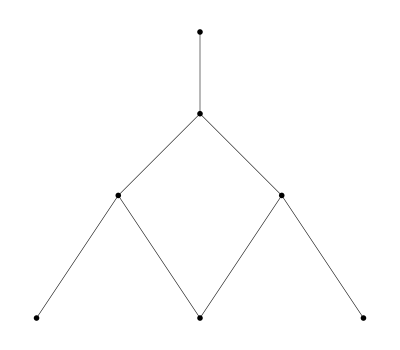

```mathematica
BratteliDiagramSn[3,Output->Graph]
```

the path corresponding the standard Young tableau {{1,2},{3}} is

```mathematica
BratteliPathSn[{{1,2},{3}}]
```

{{1},{2},{2,1}}

and the associated semi normal Young unit is

```mathematica
PermutationProduct[CentralYoungProjector[{1}],CentralYoungProjector[{2}],CentralYoungProjector[{2,1}]]//Expand
SemiNormalYoungUnit[{{1,2},{3}}]===%
```

(System`Cycles[{}])/3+1/3 System`Cycles[{{1,2}}]-1/6 System`Cycles[{{1,3}}]-1/6 System`Cycles[{{2,3}}]-1/6 System`Cycles[{{1,2,3}}]-1/6 System`Cycles[{{1,3,2}}]

True

```mathematica
StandardTableaux[3]
GLIrreducibleProject[T3[-i1,-i2,-i3],#,{-i1,-i2,-i3},Method->SemiNormalYoungUnit]&/@%
```

{{{1,2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

{1/6 T3 |   |   |  
i1 | i2 | i3+1/6 T3 |   |   |  
i1 | i3 | i2+1/6 T3 |   |   |  
i2 | i1 | i3+1/6 T3 |   |   |  
i2 | i3 | i1+1/6 T3 |   |   |  
i3 | i1 | i2+1/6 T3 |   |   |  
i3 | i2 | i1,1/3 T3 |   |   |  
i1 | i2 | i3-1/6 T3 |   |   |  
i1 | i3 | i2+1/3 T3 |   |   |  
i2 | i1 | i3-1/6 T3 |   |   |  
i2 | i3 | i1-1/6 T3 |   |   |  
i3 | i1 | i2-1/6 T3 |   |   |  
i3 | i2 | i1,1/3 T3 |   |   |  
i1 | i2 | i3+1/6 T3 |   |   |  
i1 | i3 | i2-1/3 T3 |   |   |  
i2 | i1 | i3-1/6 T3 |   |   |  
i2 | i3 | i1-1/6 T3 |   |   |  
i3 | i1 | i2+1/6 T3 |   |   |  
i3 | i2 | i1,1/6 T3 |   |   |  
i1 | i2 | i3-1/6 T3 |   |   |  
i1 | i3 | i2-1/6 T3 |   |   |  
i2 | i1 | i3+1/6 T3 |   |   |  
i2 | i3 | i1+1/6 T3 |   |   |  
i3 | i1 | i2-1/6 T3 |   |   |  
i3 | i2 | i1}

```mathematica
StandardTableaux[3]
GLIrreducibleProject[T3[-i1,-i2,-i3],#,{-i1,-i2,-i3},Method->YoungSymmetrizer]&/@%
```

{{{1,2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

OptionValue::nodef: Unknown option Method for {YoungSymmetrizer}.

OptionValue::nodef: Unknown option ManifestSym for {YoungSymmetrize}.

OptionValue::nodef: Unknown option Method for {YoungSymmetrizer}.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

{1/6 T3 |   |   |  
i1 | i2 | i3+1/6 T3 |   |   |  
i1 | i3 | i2+1/6 T3 |   |   |  
i2 | i1 | i3+1/6 T3 |   |   |  
i2 | i3 | i1+1/6 T3 |   |   |  
i3 | i1 | i2+1/6 T3 |   |   |  
i3 | i2 | i1,1/3 T3 |   |   |  
i1 | i2 | i3+1/3 T3 |   |   |  
i2 | i1 | i3-1/3 T3 |   |   |  
i3 | i1 | i2-1/3 T3 |   |   |  
i3 | i2 | i1,1/3 T3 |   |   |  
i1 | i2 | i3-1/3 T3 |   |   |  
i2 | i1 | i3-1/3 T3 |   |   |  
i2 | i3 | i1+1/3 T3 |   |   |  
i3 | i2 | i1,1/6 T3 |   |   |  
i1 | i2 | i3-1/6 T3 |   |   |  
i1 | i3 | i2-1/6 T3 |   |   |  
i2 | i1 | i3+1/6 T3 |   |   |  
i2 | i3 | i1+1/6 T3 |   |   |  
i3 | i1 | i2-1/6 T3 |   |   |  
i3 | i2 | i1}

```mathematica
(***************************)
(*** Torsion type tensor ***)
(***************************)
```

One need to be careful with indices when the tensor we what to decompose has some symmetry.

```mathematica
DefTensor[Torsion1[-i1,-i2,-i3],M,Antisymmetric[{1,2}],PrintAs->"T1"]
DefTensor[Torsion2[-i1,-i2,-i3],M,Antisymmetric[{2,3}],PrintAs->"T2"]
```

** DefTensor: Defining tensor Torsion1[-i1,-i2,-i3].

** DefTensor: Defining tensor Torsion2[-i1,-i2,-i3].

```mathematica
GLIrrepsOfTensor[Torsion1[-i1,-i2,-i3]]
GLIrrepsOfTensor[Torsion2[-i1,-i2,-i3]]
```

{{2,1},{1,1,1}}

{{2,1},{1,1,1}}

```mathematica
StandardTableaux[3]
ToCanonical[GLIrreducibleProject[Torsion1[-i1,-i2,-i3],#,{-i1,-i2,-i3},Method->SemiNormalYoungUnit]]&/@%
```

{{{1,2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

{0,0,2/3 T1 |   |   |  
i1 | i2 | i3+1/3 T1 |   |   |  
i1 | i3 | i2-1/3 T1 |   |   |  
i2 | i3 | i1,1/3 T1 |   |   |  
i1 | i2 | i3-1/3 T1 |   |   |  
i1 | i3 | i2+1/3 T1 |   |   |  
i2 | i3 | i1}

```mathematica
(******** If we project T2 it seems that we don't have the same number of irreducible components **********)
```

```mathematica
StandardTableaux[3]
ToCanonical[GLIrreducibleProject[Torsion2[-i1,-i2,-i3],#,{-i1,-i2,-i3},Method->SemiNormalYoungUnit]]&/@%
```

{{{1,2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

{0,1/2 T2 |   |   |  
i1 | i2 | i3+1/2 T2 |   |   |  
i2 | i1 | i3,1/6 T2 |   |   |  
i1 | i2 | i3-1/6 T2 |   |   |  
i2 | i1 | i3-1/3 T2 |   |   |  
i3 | i1 | i2,1/3 T2 |   |   |  
i1 | i2 | i3-1/3 T2 |   |   |  
i2 | i1 | i3+1/3 T2 |   |   |  
i3 | i1 | i2}

```mathematica
(**** but the two components 1/2 {{T2, {{, , }, {i1, i2, i3}}}}+1/2 {{T2, {{, , }, {i2, i1, i3}}}} and 1/6 {{T2, {{, , }, {i1, i2, i3}}}}-1/6 {{T2, {{, , }, {i2, i1, i3}}}}-1/3 {{T2, {{, , }, {i3, i1, i2}}}} are related by the action of the symmetric group algebra ... ***)
```

```mathematica
ToCanonical[1/3*Antisymmetrize[ToCanonical[GLIrreducibleProject[Torsion2[-i1,-i2,-i3],{{1,2},{3}},{-i1,-i2,-i3},Method->SemiNormalYoungUnit]],{-i2,-i3}]]
ToCanonical[Antisymmetrize[ToCanonical[GLIrreducibleProject[Torsion2[-i1,-i2,-i3],{{1,3},{2}},{-i1,-i2,-i3},Method->SemiNormalYoungUnit]],{-i2,-i3}]]
```

1/6 T2 |   |   |  
i1 | i2 | i3+1/12 T2 |   |   |  
i2 | i1 | i3-1/12 T2 |   |   |  
i3 | i1 | i2

1/6 T2 |   |   |  
i1 | i2 | i3+1/12 T2 |   |   |  
i2 | i1 | i3-1/12 T2 |   |   |  
i3 | i1 | i2

```mathematica
(****  we have used a basis which makes the result not explicit ***)
```

In this example you can choose a more explicit basis by selecting the appropriate indices in the input of GLIrreducibleProject

```mathematica
StandardTableaux[3]
GLIrreducibleProject[Torsion2[-i1,-i2,-i3],#,{-i2,-i3,-i1},Method->SemiNormalYoungUnit]&/@%
Map[ToCanonical[#]&,%]
```

{{{1,2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

{0,1/3 T2 |   |   |  
i1 | i2 | i3+1/3 T2 |   |   |  
i1 | i3 | i2-1/6 T2 |   |   |  
i2 | i1 | i3-1/6 T2 |   |   |  
i2 | i3 | i1-1/6 T2 |   |   |  
i3 | i1 | i2-1/6 T2 |   |   |  
i3 | i2 | i1,1/3 T2 |   |   |  
i1 | i2 | i3-1/3 T2 |   |   |  
i1 | i3 | i2+1/6 T2 |   |   |  
i2 | i1 | i3-1/6 T2 |   |   |  
i2 | i3 | i1-1/6 T2 |   |   |  
i3 | i1 | i2+1/6 T2 |   |   |  
i3 | i2 | i1,1/6 T2 |   |   |  
i1 | i2 | i3-1/6 T2 |   |   |  
i1 | i3 | i2-1/6 T2 |   |   |  
i2 | i1 | i3+1/6 T2 |   |   |  
i2 | i3 | i1+1/6 T2 |   |   |  
i3 | i1 | i2-1/6 T2 |   |   |  
i3 | i2 | i1}

{0,0,2/3 T2 |   |   |  
i1 | i2 | i3+1/3 T2 |   |   |  
i2 | i1 | i3-1/3 T2 |   |   |  
i3 | i1 | i2,1/3 T2 |   |   |  
i1 | i2 | i3-1/3 T2 |   |   |  
i2 | i1 | i3+1/3 T2 |   |   |  
i3 | i1 | i2}

Note that because the multiplicity of each irreps present in the torsion tensor is 1  GLCentralIrreducibleProject yield the same result

```mathematica
IntegerPartitions[3]
ToCanonical[GLCentralIrreducibleProject[Torsion2[-i1,-i2,-i3],#]]&/@%//Expand
```

{{3},{2,1},{1,1,1}}

{0,2/3 T2 |   |   |  
i1 | i2 | i3+1/3 T2 |   |   |  
i2 | i1 | i3-1/3 T2 |   |   |  
i3 | i1 | i2,1/3 T2 |   |   |  
i1 | i2 | i3-1/3 T2 |   |   |  
i2 | i1 | i3+1/3 T2 |   |   |  
i3 | i1 | i2}

### 2. O(dim) irreducible decomposition of a tensor

```mathematica
(*******************************************************************)
(******* Decomposition of an arbitrary tensor of order 2 ***********)
(*******************************************************************)
```

```mathematica
BratteliDiagramBn[2,Output->Graph,VertexSize->0.045,ImageSize->350]
```

-Graphics-

```mathematica
?OCentralIrreducibleProject
```

```mathematica
?OIrrepsOfTensor
```

```mathematica
IrrepsOfBrauer[2]
OIrrepsOfTensor[T2[-i1,-i2]]
```

{{},{2},{1,1}}

{{},{2},{1,1}}

```mathematica
OIrrepsOfTensor[T2[-i1,-i2]]
```

{{},{2},{1,1}}

```mathematica
OIrrepsOfTensor[T2[-i1,-i2]]
OCentralIrreducibleProject[T2[-i1,-i2],#,g]&/@%
Total[%]
```

{{},{2},{1,1}}

{(g |   |  
i1 | i2 T2 |   | i10
i10 |)/d,(T2 |   |  
i1 | i2)/2-(g |   |  
i1 | i2 T2 |   | i10
i10 |)/d+(T2 |   |  
i2 | i1)/2,(T2 |   |  
i1 | i2)/2-(T2 |   |  
i2 | i1)/2}

T2 |   |  
i1 | i2

```mathematica
BratteliDiagramBn[2]
OIrreducibleProject[T2[-i1,-i2],#,g]&/@%
```

{{{1},{}},{{1},{2}},{{1},{1,1}}}

{(g |   |  
i1 | i2 T2 |   | i10
i10 |)/d,(T2 |   |  
i1 | i2)/2-(g |   |  
i1 | i2 T2 |   | i10
i10 |)/d+(T2 |   |  
i2 | i1)/2,(T2 |   |  
i1 | i2)/2-(T2 |   |  
i2 | i1)/2}

```mathematica
(******* Decomposition of an arbitrary tensor of order 3 ***********)
```

```mathematica
BratteliDiagramBn[3,Output->Graph,VertexSize->0.04,ImageSize->500]
```

-Graphics-

The multiplicity of an orthogonal irrep is equal to the number of path leading to this irrep in the Bratteli diagram of the Brauer algebra. This is due to the Schur-Weyl duality between the Orthogonal group and the Brauer algebra.

```mathematica
OIrrepsOfTensor[T3[-i1,-i2,-i3]]
```

{{1},{1},{1},{3},{2,1},{2,1},{1,1,1}}

```mathematica
?OCentralIrreducibleProject
```

```mathematica
IrrepsOfBrauer[3]
OCentralIrreducibleProject[T3[-i1,-i2,-i3],#]&/@%
Collect[Total[%]//ToCanonical,{_T3,_g},Factor]
```

{{1},{3},{2,1},{1,1,1}}

{g |   |  
i2 | i3 (((1+d) T3 |   |   | i12
i1 | i12 |)/((-1+d) (2+d))-(T3 |   |   | i10
i10 | i1 |)/((-1+d) (2+d))-(T3 |   | i11 |  
i11 |   | i1)/((-1+d) (2+d)))+g |   |  
i1 | i3 (-(T3 |   | i11 |  
i11 |   | i2)/((-1+d) (2+d))+((1+d) T3 |   |   | i12
i12 | i2 |)/((-1+d) (2+d))-(T3 |   |   | i10
i2 | i10 |)/((-1+d) (2+d)))+g |   |  
i1 | i2 (-(T3 |   |   | i11
i11 | i3 |)/((-1+d) (2+d))+((1+d) T3 |   | i12 |  
i12 |   | i3)/((-1+d) (2+d))-(T3 |   |   | i10
i3 | i10 |)/((-1+d) (2+d))),1/6 T3 |   |   |  
i1 | i2 | i3+1/6 T3 |   |   |  
i1 | i3 | i2+g |   |  
i2 | i3 (-(T3 |   |   | i12
i1 | i12 |)/(3 (2+d))-(T3 |   |   | i10
i10 | i1 |)/(3 (2+d))-(T3 |   | i11 |  
i11 |   | i1)/(3 (2+d)))+1/6 T3 |   |   |  
i2 | i1 | i3+g |   |  
i1 | i3 (-(T3 |   | i11 |  
i11 |   | i2)/(3 (2+d))-(T3 |   |   | i12
i12 | i2 |)/(3 (2+d))-(T3 |   |   | i10
i2 | i10 |)/(3 (2+d)))+1/6 T3 |   |   |  
i2 | i3 | i1+1/6 T3 |   |   |  
i3 | i1 | i2+g |   |  
i1 | i2 (-(T3 |   |   | i11
i11 | i3 |)/(3 (2+d))-(T3 |   | i12 |  
i12 |   | i3)/(3 (2+d))-(T3 |   |   | i10
i3 | i10 |)/(3 (2+d)))+1/6 T3 |   |   |  
i3 | i2 | i1,2/3 T3 |   |   |  
i1 | i2 | i3+g |   |  
i2 | i3 (-(2 T3 |   |   | i12
i1 | i12 |)/(3 (-1+d))+(T3 |   |   | i10
i10 | i1 |)/(3 (-1+d))+(T3 |   | i11 |  
i11 |   | i1)/(3 (-1+d)))+g |   |  
i1 | i3 ((T3 |   | i11 |  
i11 |   | i2)/(3 (-1+d))-(2 T3 |   |   | i12
i12 | i2 |)/(3 (-1+d))+(T3 |   |   | i10
i2 | i10 |)/(3 (-1+d)))-1/3 T3 |   |   |  
i2 | i3 | i1-1/3 T3 |   |   |  
i3 | i1 | i2+g |   |  
i1 | i2 ((T3 |   |   | i11
i11 | i3 |)/(3 (-1+d))-(2 T3 |   | i12 |  
i12 |   | i3)/(3 (-1+d))+(T3 |   |   | i10
i3 | i10 |)/(3 (-1+d))),1/6 T3 |   |   |  
i1 | i2 | i3-1/6 T3 |   |   |  
i1 | i3 | i2-1/6 T3 |   |   |  
i2 | i1 | i3+1/6 T3 |   |   |  
i2 | i3 | i1+1/6 T3 |   |   |  
i3 | i1 | i2-1/6 T3 |   |   |  
i3 | i2 | i1}

T3 |   |   |  
i1 | i2 | i3

```mathematica
?OIrreducibleProject
```

```mathematica
BratteliDiagramBn[3]
OIrreducibleProject[T3[-i1,-i2,-i3],#]&/@%
Collect[Total[%]//ToCanonical,{_T3,_g},Factor]
```

{{{1},{},{1}},{{1},{2},{1}},{{1},{2},{2,1}},{{1},{2},{3}},{{1},{1,1},{1}},{{1},{1,1},{2,1}},{{1},{1,1},{1,1,1}}}

{(g |   |  
i1 | i2 T3 |   | i10 |  
i10 |   | i3)/d,g |   |  
i2 | i3 ((d T3 |   |   | i10
i1 | i10 |)/(2 (-1+d) (2+d))+(d T3 |   |   | i11
i11 | i1 |)/(2 (-1+d) (2+d))-(T3 |   | i12 |  
i12 |   | i1)/((-1+d) (2+d)))+g |   |  
i1 | i3 ((d T3 |   |   | i11
i11 | i2 |)/(2 (-1+d) (2+d))-(T3 |   | i12 |  
i12 |   | i2)/((-1+d) (2+d))+(d T3 |   |   | i10
i2 | i10 |)/(2 (-1+d) (2+d)))+g |   |  
i1 | i2 (-(T3 |   |   | i11
i11 | i3 |)/((-1+d) (2+d))+(2 T3 |   | i12 |  
i12 |   | i3)/((-1+d) d (2+d))-(T3 |   |   | i10
i3 | i10 |)/((-1+d) (2+d))),1/3 T3 |   |   |  
i1 | i2 | i3-1/6 T3 |   |   |  
i1 | i3 | i2+g |   |  
i2 | i3 (-(T3 |   |   | i10
i1 | i10 |)/(6 (-1+d))-(T3 |   |   | i11
i11 | i1 |)/(6 (-1+d))+(T3 |   | i12 |  
i12 |   | i1)/(3 (-1+d)))+1/3 T3 |   |   |  
i2 | i1 | i3+g |   |  
i1 | i3 (-(T3 |   |   | i11
i11 | i2 |)/(6 (-1+d))+(T3 |   | i12 |  
i12 |   | i2)/(3 (-1+d))-(T3 |   |   | i10
i2 | i10 |)/(6 (-1+d)))-1/6 T3 |   |   |  
i2 | i3 | i1-1/6 T3 |   |   |  
i3 | i1 | i2+g |   |  
i1 | i2 ((T3 |   |   | i11
i11 | i3 |)/(3 (-1+d))-(2 T3 |   | i12 |  
i12 |   | i3)/(3 (-1+d))+(T3 |   |   | i10
i3 | i10 |)/(3 (-1+d)))-1/6 T3 |   |   |  
i3 | i2 | i1,1/6 T3 |   |   |  
i1 | i2 | i3+1/6 T3 |   |   |  
i1 | i3 | i2+g |   |  
i2 | i3 (-(T3 |   |   | i10
i1 | i10 |)/(3 (2+d))-(T3 |   |   | i11
i11 | i1 |)/(3 (2+d))-(T3 |   | i12 |  
i12 |   | i1)/(3 (2+d)))+1/6 T3 |   |   |  
i2 | i1 | i3+g |   |  
i1 | i3 (-(T3 |   |   | i11
i11 | i2 |)/(3 (2+d))-(T3 |   | i12 |  
i12 |   | i2)/(3 (2+d))-(T3 |   |   | i10
i2 | i10 |)/(3 (2+d)))+1/6 T3 |   |   |  
i2 | i3 | i1+1/6 T3 |   |   |  
i3 | i1 | i2+g |   |  
i1 | i2 (-(T3 |   |   | i11
i11 | i3 |)/(3 (2+d))-(T3 |   | i12 |  
i12 |   | i3)/(3 (2+d))-(T3 |   |   | i10
i3 | i10 |)/(3 (2+d)))+1/6 T3 |   |   |  
i3 | i2 | i1,g |   |  
i2 | i3 ((T3 |   |   | i10
i1 | i10 |)/(2 (-1+d))-(T3 |   |   | i11
i11 | i1 |)/(2 (-1+d)))+g |   |  
i1 | i3 ((T3 |   |   | i11
i11 | i2 |)/(2 (-1+d))-(T3 |   |   | i10
i2 | i10 |)/(2 (-1+d))),1/3 T3 |   |   |  
i1 | i2 | i3+1/6 T3 |   |   |  
i1 | i3 | i2+g |   |  
i2 | i3 (-(T3 |   |   | i10
i1 | i10 |)/(2 (-1+d))+(T3 |   |   | i11
i11 | i1 |)/(2 (-1+d)))-1/3 T3 |   |   |  
i2 | i1 | i3+g |   |  
i1 | i3 (-(T3 |   |   | i11
i11 | i2 |)/(2 (-1+d))+(T3 |   |   | i10
i2 | i10 |)/(2 (-1+d)))-1/6 T3 |   |   |  
i2 | i3 | i1-1/6 T3 |   |   |  
i3 | i1 | i2+1/6 T3 |   |   |  
i3 | i2 | i1,1/6 T3 |   |   |  
i1 | i2 | i3-1/6 T3 |   |   |  
i1 | i3 | i2-1/6 T3 |   |   |  
i2 | i1 | i3+1/6 T3 |   |   |  
i2 | i3 | i1+1/6 T3 |   |   |  
i3 | i1 | i2-1/6 T3 |   |   |  
i3 | i2 | i1}

T3 |   |   |  
i1 | i2 | i3

```mathematica
(******* "Central" irreducible decomposition of an arbitrary tensor of order 4 ***********)
```

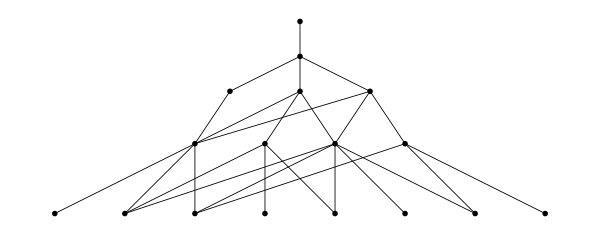

```mathematica
BratteliDiagramBn[4,Output->Graph,VertexSize->0.017,ImageSize->600]
```

```mathematica
OIrrepsOfTensor[T4[-i1,-i2,-i3,-i4]]
```

{{},{},{},{2},{2},{2},{2},{2},{2},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{4},{2,2},{2,2},{3,1},{3,1},{3,1},{2,1,1},{2,1,1},{2,1,1},{1,1,1,1}}

```mathematica
BratteliDiagramBn[4,Output->Graph,VertexSize->0.017,ImageSize->600]
```

-Graphics-

```mathematica
OIrrepsOfTensor[T4[-i1,-i2,-i3,-i4]]
```

{{},{},{},{2},{2},{2},{2},{2},{2},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{4},{2,2},{2,2},{3,1},{3,1},{3,1},{2,1,1},{2,1,1},{2,1,1},{1,1,1,1}}

```mathematica
IrrepsOfBrauer[4]
CentralDecompositionT4=OCentralIrreducibleProject[T4[-i1,-i2,-i3,-i4],#]&/@%;
Collect[Total[%]//ToCanonical,{_T4,_g},Factor]
```

{{},{2},{1,1},{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

T4 |   |   |   |  
i1 | i2 | i3 | i4

```mathematica
BratteliDiagramBn[4]
OirrDecompositionT4=OIrreducibleProject[T4[-i1,-i2,-i3,-i4],#]&/@%
Collect[Total[%]//ToCanonical,{_T4,_g},Factor]
```

{{{1},{},{1},{}},{{1},{},{1},{2}},{{1},{},{1},{1,1}},{{1},{2},{1},{}},{{1},{2},{1},{2}},{{1},{2},{1},{1,1}},{{1},{2},{2,1},{2}},{{1},{2},{2,1},{1,1}},{{1},{2},{2,1},{2,1,1}},{{1},{2},{2,1},{3,1}},{{1},{2},{2,1},{2,2}},{{1},{2},{3},{2}},{{1},{2},{3},{3,1}},{{1},{2},{3},{4}},{{1},{1,1},{1},{}},{{1},{1,1},{1},{2}},{{1},{1,1},{1},{1,1}},{{1},{1,1},{2,1},{2}},{{1},{1,1},{2,1},{1,1}},{{1},{1,1},{2,1},{2,1,1}},{{1},{1,1},{2,1},{3,1}},{{1},{1,1},{2,1},{2,2}},{{1},{1,1},{1,1,1},{1,1}},{{1},{1,1},{1,1,1},{2,1,1}},{{1},{1,1},{1,1,1},{1,1,1,1}}}

$Aborted

ToCanonical::noident: Unknown expression not canonicalized: Total[$Aborted] .

Total[$Aborted]

```mathematica
(***** Irreducible decomposition of the metric Riemann tensor : Ricci decomposition *****)
```

```mathematica
GLIrrepsOfTensor[Riemanncd[-i1,-i2,-i3,-i4]]
```

{{2,2},{2,1,1},{1,1,1,1}}

This result is not entirely correct. This is due to the limitations of GLIrrepsOfTensor. The only irrep corresponding to the space of metric Riemann tensor is {2,2}.

```mathematica
?GLIrrepsOfTensor
```

```mathematica
Riemanncd/:GLIrrepsOfTensor[Riemanncd[inds__]]:={{2,2}}
```

```mathematica
GLIrrepsOfTensor[Riemanncd[-i1,-i2,-i3,-i4]]
```

{{2,2}}

```mathematica
BranchingRule[{2,2},GeneralLinearGroup,OrthogonalGroup]
```

{{},{2},{2,2}}

We can use the function OCentralIrreducibleProject to perform the irreducible decomposition of the Riemann tensor because the multiplicity of each irreps is 1.

```mathematica
?OCentralIrreducibleProject
```

```mathematica
OCentralIrreducibleProject[Riemanncd[-i1,-i2,-i3,-i4],{2,2}]//ToCanonical
OCentralIrreducibleProject[Riemanncd[-i1,-i2,-i3,-i4],{2}]//ToCanonical
OCentralIrreducibleProject[Riemanncd[-i1,-i2,-i3,-i4],{}]//ToCanonical
```

-(g |   |  
i2 | i4 R[∇^(g)] |   |  
i1 | i3)/(-2+d)+(g |   |  
i2 | i3 R[∇^(g)] |   |  
i1 | i4)/(-2+d)+(g |   |  
i1 | i4 R[∇^(g)] |   |  
i2 | i3)/(-2+d)-(g |   |  
i1 | i3 R[∇^(g)] |   |  
i2 | i4)/(-2+d)-(g |   |  
i1 | i4 g |   |  
i2 | i3 R[∇^(g)])/((-2+d) (-1+d))+(g |   |  
i1 | i3 g |   |  
i2 | i4 R[∇^(g)])/((-2+d) (-1+d))+2/3 R[∇^(g)] |   |   |   |  
i1 | i2 | i3 | i4+1/3 R[∇^(g)] |   |   |   |  
i1 | i3 | i2 | i4-1/3 R[∇^(g)] |   |   |   |  
i1 | i4 | i2 | i3

(g |   |  
i2 | i4 R[∇^(g)] |   |  
i1 | i3)/(-2+d)-(g |   |  
i2 | i3 R[∇^(g)] |   |  
i1 | i4)/(-2+d)-(g |   |  
i1 | i4 R[∇^(g)] |   |  
i2 | i3)/(-2+d)+(g |   |  
i1 | i3 R[∇^(g)] |   |  
i2 | i4)/(-2+d)+(2 g |   |  
i1 | i4 g |   |  
i2 | i3 R[∇^(g)])/((-2+d) d)-(2 g |   |  
i1 | i3 g |   |  
i2 | i4 R[∇^(g)])/((-2+d) d)

-(g |   |  
i1 | i4 g |   |  
i2 | i3 R[∇^(g)])/((-1+d) d)+(g |   |  
i1 | i3 g |   |  
i2 | i4 R[∇^(g)])/((-1+d) d)